```mathematica
(* Basketball*)
```

## Get the URLs for all games in a specific month

```mathematica
(* Specify the year and month you want for example last month (november)

year = "2018";
months = {"october", "november", "december", "january", "february", "march","april"};
m = months[[2]];

this month:
*)
year = "2018";
months = {"october", "november", "december", "january", "february", "march","april"};
m = months[[3]];

mon = {"Oct", "Nov", "Dec", "Jan", "Feb", "Mar","Apr"};
gameyear = ToString[ToExpression[year] -1];
teamnames = {"Atlanta Hawks","ATL","Boston Celtics","BOS","Brooklyn Nets","BRK","Charlotte Hornets","CHO","Chicago Bulls","CHI","Cleveland Cavaliers","CLE","Dallas Mavericks","DAL","Denver Nuggets","DEN","Detroit Pistons","DET","Golden State Warriors","GSW","Houston Rockets","HOU","Indiana Pacers","IND","Los Angeles Clippers","LAC","Los Angeles Lakers","LAL","Memphis Grizzlies","MEM","Miami Heat","MIA","Milwaukee Bucks","MIL","Minnesota Timberwolves","MIN","New Orleans Pelicans","NOP","New York Knicks","NYK","Oklahoma City Thunder","OKC","Orlando Magic","ORL","Philadelphia 76ers","PHI","Phoenix Suns","PHO","Portland Trail Blazers","POR","Sacramento Kings","SAC","San Antonio Spurs","SAS","Toronto Raptors","TOR","Utah Jazz","UTA","Washington Wizards","WAS"};
teamnamesNo3lc = teamnames[[Range[Length[teamnames]/2]*2-1]];
```

```mathematica
(* create a string that is the url of schedule for the month of games we want *)
```

```mathematica
month = StringJoin["https://www.basketball-reference.com/leagues/NBA_",year,"_games-", m,".html"]
```

https://www.basketball-reference.com/leagues/NBA_2018_games-december.html

```mathematica
(* Import the data for that month*)
```

```mathematica
teams = Import[month,"Data"];
```

```mathematica
gamesplayed = {};
For[i =1, i≤ Length[teams[[4,1,3]]],i++,
If[Length[teams[[4,1,3,i]]]>5,
AppendTo[gamesplayed, i]];
]
```

```mathematica
outcomesoct = teams[[4,1,3,;;,3;;6]];
```

```mathematica
outcomesnov = teams[[4,1,3,;;,3;;6]];
```

```mathematica
outcomesdec = teams[[4,1,3,gamesplayed,3;;6]];
```

```mathematica
Length[outcomesoct]
```

104

```mathematica
Length[outcomesnov]
```

213

```mathematica
Length[outcomesdec]
```

49

```mathematica
gamesstrings = {};
(* For every game *)
For[j = 1, j ≤ Length[teams[[4,1,3]]],j++,

(* Day *)
day = StringTake[teams[[4,1,3,j,1]],StringPosition[teams[[4,1,3,j,1]],NumberString,1]][[1]];
If[ToExpression[day]<10,day = StringJoin["0",day]];
mons = {10,11,12,1,2,3,4};

(* Make sure the game has not happened yet!
If[the game your asking for is this year or before, and prior to this month OR
the this year or before and equal to this month but prior to today, then build a string thats the url for that game i.e. try to download that data.
]

*)
If[MemberQ[gamesplayed,j]

(*Today["Year"]>=ToExpression[year]-1&& Today["Month"] > mons[[Position[months,m][[1,1]]]]||Today["Year"]>=ToExpression[year]-1&&Today["Month"] == mons[[Position[months,m][[1,1]]]] && Today["Day"] > ToExpression[day]*),
(* Position of home team in team names list +1 gives location of 3 letter code*)
p = Position[teamnames,teams[[4,1,3,j,5]]][[1]][[1]] + 1;

For[i =1, i ≤ Length[mon],i++, 
If[StringContainsQ[teams[[4,1,3,j,1]],mon[[i]]],
(*dauy*)
(*Month*)
mons = {10,11,12,1,2,3,4};

AppendTo[gamesstrings,StringJoin[gameyear,ToString[mons[[i]]],day,"0", teamnames[[p]]]];
];
];
];
];
```

```mathematica
(* look in game strings *)
```

```mathematica
gamesstrings
```

{201712010CHI,201712010MEM,201712010MIA,201712010OKC,201712010ORL,201712010TOR,201712010UTA,201712010WAS,201712020BOS,201712020BRK,201712020CLE,201712020DAL,201712020DEN,201712020MIL,201712020PHI,201712020POR,201712030LAL,201712030MIA,201712030MIN,201712030NYK,201712030OKC,201712040ATL,201712040BOS,201712040CHI,201712040CHO,201712040DAL,201712040IND,201712040MEM,201712040NOP,201712040PHI,201712040SAS,201712040UTA,201712050OKC,201712050POR,201712050TOR,201712060BOS,201712060CHO,201712060CLE,201712060IND,201712060LAC,201712060MIL,201712060NOP,201712060NYK,201712060ORL,201712060SAS,201712070BRK,201712070PHI,201712070PHO,201712070UTA,201712080CHO,201712080DET,201712080IND,201712080MEM,201712080MIL,201712080NOP,201712080ORL,201712080SAS}

## Get the Game Data for a list of games

```mathematica
gamestats = {};
For[i =1, i ≤ Length[gamesstrings],i++,
Print[i," out of ",Length[gamesstrings]];
game = {};
(* make URL *)
gameurl = ToString[StringJoin["https://www.basketball-reference.com/boxscores/",gamesstrings[[i]],".html"]];
(* Import data *)
gamedata = Import[gameurl, "Data"];
(* reshape data *)
For[j =1, j ≤ 4, j++,
(* get stats  each team has regualar and advanced *)
d = gamedata[[4,j,3]];
header = gamedata[[4,j,2]][[2]];
PrependTo[d, header];
totals = gamedata[[4,j,4]];
TableForm[AppendTo[d,totals]];
AppendTo[game,d];
];
AppendTo[gamestats,game];
];
(* outcomes is the score *)
```

1 out of 57

2 out of 57

3 out of 57

4 out of 57

5 out of 57

6 out of 57

7 out of 57

8 out of 57

9 out of 57

10 out of 57

11 out of 57

12 out of 57

13 out of 57

14 out of 57

15 out of 57

16 out of 57

17 out of 57

18 out of 57

19 out of 57

20 out of 57

21 out of 57

22 out of 57

23 out of 57

24 out of 57

25 out of 57

26 out of 57

27 out of 57

28 out of 57

29 out of 57

30 out of 57

31 out of 57

32 out of 57

33 out of 57

34 out of 57

35 out of 57

36 out of 57

37 out of 57

38 out of 57

39 out of 57

40 out of 57

41 out of 57

42 out of 57

43 out of 57

44 out of 57

45 out of 57

46 out of 57

47 out of 57

48 out of 57

49 out of 57

50 out of 57

51 out of 57

52 out of 57

53 out of 57

54 out of 57

55 out of 57

56 out of 57

57 out of 57

```mathematica
outcomes = teams[[4,1,3,;;,3;;6]];
```

```mathematica
Export["/Users/David/Desktop/BasketballModel/October17gamestats.dat",gamestats,"Table"]
```

/Users/David/Desktop/BasketballModel/October17gamestats.dat

```mathematica
Export["/Users/David/Desktop/BasketballModel/November17gamestats.dat",gamestats,"Table"]
```

/Users/David/Desktop/BasketballModel/November17gamestats.dat

```mathematica
Export["/Users/David/Desktop/BasketballModel/December17gamestats.dat",gamestats,"Table"]
```

/Users/David/Desktop/BasketballModel/December17gamestats.dat

```mathematica
Export["/Users/David/Desktop/BasketballModel/October17outcomes.dat",outcomesoct,"Table"]
```

/Users/David/Desktop/BasketballModel/October17outcomes.dat

```mathematica
Export["/Users/David/Desktop/BasketballModel/November17outcomes.dat",outcomesnov,"Table"]
```

/Users/David/Desktop/BasketballModel/November17outcomes.dat

```mathematica
Export["/Users/David/Desktop/BasketballModel/December17outcomes.dat",outcomesdec,"Table"]
```

/Users/David/Desktop/BasketballModel/December17outcomes.dat

```mathematica
gamestatsimpoct= Import["/Users/David/Desktop/BasketballModel/October17gamestats.dat","TSV"];
gamestatsimpnov = Import["/Users/David/Desktop/BasketballModel/November17gamestats.dat","TSV"];
gamestatsimpdec = Import["/Users/David/Desktop/BasketballModel/December17gamestats.dat","TSV"];
```

```mathematica
outcomesimpoct= Import["/Users/David/Desktop/BasketballModel/October17outcomes.dat","TSV"];
outcomesimpnov = Import["/Users/David/Desktop/BasketballModel/November17outcomes.dat","TSV"];
outcomesimpdec = Import["/Users/David/Desktop/BasketballModel/December17outcomes.dat","TSV"];
```

```mathematica
gamestatsimpoct = ToExpression[gamestatsimpoct] ;
gamestatsimpnov = ToExpression[gamestatsimpnov] ;
gamestatsimpdec = ToExpression[gamestatsimpdec] ;
```

```mathematica
gamestats = Join[gamestatsimpoct,gamestatsimpnov,gamestatsimpdec];
```

```mathematica
outcomes = Join[outcomesimpoct,outcomesimpnov,outcomesimpdec];
```

```mathematica
(* The 19th game that month.*)
```

```mathematica
Length[gamestats]
```

374

```mathematica
Length[outcomes]
```

374

## Building the model

```mathematica
gamindices = {};
For[i = 1, i ≤ Length[teamnamesNo3lc],i++,
AppendTo[gamindices,Position[outcomes,teamnamesNo3lc[[i]]][[6,1]]]
]
```

```mathematica
t = Range[Max[gamindices], Length[outcomes]-50]
```

{111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324}

```mathematica
Length[t]
```

214

```mathematica
(* given a game number it spits out the game number of the past 5 games *)
past5[gamenumber_]:= Return[
(* given a game number get the game numbers of the past 5 games of the home team and of the away team *)
hometeamGamesThatMonth = Position[
outcomes,outcomes[[gamenumber,3]]
];
homegameposition = Position[hometeamGamesThatMonth,gamenumber][[1,1]];
past5homegames = hometeamGamesThatMonth[[Range[homegameposition-6,homegameposition-1]]];

awayteamGamesThatMonth = Position[
outcomes,outcomes[[gamenumber,1]]
];
awaygameposition = Position[awayteamGamesThatMonth,gamenumber][[1,1]];
past5awaygames = awayteamGamesThatMonth[[Range[awaygameposition-5,awaygameposition-1]]];

];
```

```mathematica
(* Returns outcome from home and away teams. *)
```

```mathematica
out[gn_]:=Return[

outcomeaway = gamestats[[gn,{1,2},{1,-1}]];
outcomeaway[[2,2,-3]] =1;
outcomeaway = outcomeaway[[;;,2, 3;;]];
outcomeaway = Flatten[outcomeaway];

outcomehome = gamestats[[gn,{3,4},{1,-1}]];
outcomehome[[2,2,-3]] =3;
outcomehome = outcomehome[[;;,2, 3;;]];
outcomehome = Flatten[outcomehome];

Join[outcomehome, outcomeaway]
];
```

```mathematica
(* Vector of past 5 games *)
```

```mathematica
past5vector[past5games_]:=Return[
past5gameslist = {};
For[j = 1, j≤5 , ++j,
homeoraway = past5games[[j,2]];
If[homeoraway ==1, c = {1,2},c = {3,4}];
outcome = gamestats[[past5games[[j,1]],c,{1,-1}]];
outcome[[2,2,-3]] =homeoraway;
(*outcome = outcome[[;;,2, 3;;]];*)
AppendTo[past5gameslist, outcome];
 ];
linearweights = {.11,.14,.21,.24,.3};
last5outcomevector = Dot[linearweights,Table[Flatten[past5gameslist[[k,{1,2},2,3;;]]],{k,1,5}]]
(*last5outcomevector = Flatten[{Dot[linearweights,Table[Flatten[past5gameslist[[k,{1,2},2,3;;]]],{k,1,5}]],
Dot[linearweights,Table[Flatten[past5gameslist[[k,{1,2},2,3;;]]],{k,1,5}]]}]*)

];
```

```mathematica
outcomesmat = {};
outcomeslast5mat = {};
Length[t]

For[i = 1, i ≤ Length[t],i++, 
Clear[gamenumber];
gamenumber = t[[i]];
past5[gamenumber];
pastvect = Join[past5vector[past5awaygames],past5vector[past5homegames]];
AppendTo[outcomeslast5mat,pastvect];
AppendTo[outcomesmat,out[gamenumber]];
]
```

214

```mathematica
MatrixForm[outcomesmat];
```

## Linear Model For Points

```mathematica
(* Linear Model For Pts*)
output = outcomesmat[[;;,18]];
inputs = outcomeslast5mat;
data = Table[AppendTo[inputs[[j]],output[[j]]],{j,1,Length[output]}];
lmpts = LinearModelFit[data,Table[Subscript[x, n],{n,1,64}],Table[Subscript[x, n],{n,1,64}]]
```

FittedModel[-124.07+1.70668×10^13 x_1+2.92546 x_2+1663.4 x_3+«94»+4.51633 x_63+0.191114 x_64]

```mathematica
(* Linear Model for Opponents Pts *)
```

```mathematica
output = outcomesmat[[;;,18+32]];
inputs = outcomeslast5mat;
data = Table[AppendTo[inputs[[j]],output[[j]]],{j,1,Length[output]}];
lmopppts = LinearModelFit[data,Table[Subscript[x, n],{n,1,64}],Table[Subscript[x, n],{n,1,64}]]
```

FittedModel[-732.076+8.81413×10^12 x_1+5.98914 x_2+5703.72 x_3+«92»]

```mathematica
TableForm[{output,Table[lmopppts@@inputs[[i,;;64]],{i,1,100}]}]
```

91 | 104 | 119 | 109 | 103 | 122 | 110 | 112 | 119 | 99 | 94 | 96 | 112 | 107 | 101 | 105 | 110 | 101 | 109 | 130 | 96 | 127 | 99 | 113 | 99 | 117 | 110 | 104 | 102 | 94 | 101 | 104 | 99 | 95 | 107 | 110 | 80 | 98 | 119 | 104 | 117 | 113 | 98 | 86 | 107 | 114 | 104 | 113 | 96 | 97 | 101 | 99 | 126 | 94 | 113 | 108 | 118 | 95 | 87 | 105 | 104 | 111 | 128 | 101 | 94 | 84 | 111 | 107 | 114 | 96 | 90 | 103 | 91 | 110 | 94 | 106 | 94 | 94 | 103 | 118 | 99 | 100 | 109 | 103 | 105 | 104 | 100 | 82 | 109 | 92 | 109 | 97 | 129 | 80 | 115 | 115 | 116 | 102 | 95 | 86 | 125 | 101 | 79 | 94 | 88 | 142 | 107 | 120 | 113 | 111 | 114 | 100 | 122 | 82 | 101 | 84 | 91 | 110 | 87 | 79 | 105 | 125 | 124 | 90 | 118 | 109 | 120 | 100 | 105 | 91 | 102 | 110 | 116 | 100 | 99 | 107 | 85 | 105 | 86 | 114 | 85 | 94 | 116 | 124 | 109 | 95 | 95 | 98 | 118 | 90 | 100 | 91 | 81 | 113 | 102 | 80 | 104 | 103 | 127 | 99 | 92 | 94 | 104 | 109 | 99 | 115 | 112 | 106 | 81 | 95 | 102 | 108 | 111 | 97 | 108 | 108 | 100 | 98 | 108 | 118 | 110 | 103 | 109 | 115 | 103 | 113 | 108 | 104 | 97 | 92 | 112 | 77 | 109 | 107 | 97 | 127 | 120 | 86 | 108 | 113 | 95 | 113 | 121 | 97 | 110 | 126 | 103 | 107 | 95 | 100 | 107 | 133 | 115 | 108
116.843 | 110.982 | 131.543 | 103.415 | 108.182 | 114.046 | 98.6656 | 108.429 | 119.347 | 106.879 | 103.794 | 104.741 | 106.437 | 100.979 | 101.265 | 118.536 | 112.378 | 107.597 | 101.525 | 122.177 | 100.922 | 116.506 | 102.022 | 109.244 | 95.7988 | 114.968 | 114.066 | 104.134 | 114.298 | 103.147 | 104.707 | 105.85 | 100.605 | 108.078 | 108.229 | 101.199 | 106.791 | 106.731 | 105.557 | 108.373 | 106.047 | 100.95 | 96.1601 | 97.6678 | 105.315 | 103.257 | 97.6704 | 105.331 | 101.197 | 102.346 | 102.07 | 111.199 | 110.527 | 104.032 | 108.867 | 102.797 | 114.681 | 106.098 | 97.3754 | 103.973 | 106.226 | 110.322 | 112.095 | 108.235 | 102.465 | 100.721 | 102.415 | 111.99 | 100.633 | 108.125 | 94.6046 | 107.986 | 97.7186 | 105.811 | 95.2385 | 114.909 | 106.946 | 103.405 | 101.097 | 111.422 | 106.572 | 111.967 | 102.61 | 100.169 | 117.466 | 99.661 | 104.953 | 100.726 | 95.8363 | 100.331 | 113.721 | 108.815 | 110.555 | 107.112 | 107.655 | 116.358 | 107.593 | 96.189 | 99.4132 | 97.2628 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

## Validation

```mathematica
outcomesmat = {};
outcomeslast5mat = {};
t = Range[Max[gamindices],Length[outcomes]];

For[i = 1, i ≤ Length[t],i++, 
Clear[gamenumber];
gamenumber = t[[i]];
past5[gamenumber];
pastvect = Join[past5vector[past5awaygames],past5vector[past5homegames]];
AppendTo[outcomeslast5mat,pastvect];
AppendTo[outcomesmat,out[gamenumber]];
]
```

```mathematica
predictedoutcome = lmpts@@@outcomeslast5mat - lmopppts@@@outcomeslast5mat
```

{-4.61149,-0.27753,-23.4153,9.18927,-1.79837,-6.358,8.87527,-3.2895,-27.4346,-5.00637,-5.03843,-5.4594,9.18746,9.79457,-2.52768,-7.36583,3.29009,8.53468,-2.71099,-8.40874,3.32597,-9.62151,19.2074,-0.836468,14.1706,12.3317,4.77256,-2.19211,-6.48983,15.2249,10.8225,-2.66583,3.11844,5.52522,-3.89239,5.69209,2.12611,-1.679,-0.4464,3.5554,1.29424,9.40575,-2.01526,-2.89176,10.5604,13.3131,13.8906,6.89265,0.14412,5.84754,13.2931,-2.12525,-3.80155,7.96434,0.632131,1.6749,-5.54,-0.310523,6.17039,-2.60073,8.83464,-0.27818,-6.74226,-5.33137,-5.41732,-2.02429,-3.24716,11.7322,18.5861,0.390693,8.39284,2.36697,22.045,-3.83447,15.5034,-9.98029,8.26179,-7.66176,3.96781,-14.1086,-1.86805,10.1048,9.65957,7.58711,0.143079,0.797944,-5.83225,-2.44673,2.81091,5.73462,0.328274,-10.4722,8.74066,8.16687,-2.65479,-1.1399,3.24854,-3.24041,4.28771,9.32679,-6.90364,8.15144,1.33429,-9.58745,-11.2529,-26.7771,-1.00738,3.33965,5.83842,8.06521,15.341,-1.04992,3.29918,-3.54887,-8.57617,10.9236,4.49422,-2.90947,5.97022,5.54057,-21.6393,-5.23374,0.487706,2.54484,-3.55981,-5.88937,3.85995,4.23841,-5.86345,10.7991,-2.94535,-4.92741,1.92996,9.65413,5.17767,5.86284,12.495,-2.97813,-0.165536,-10.4919,8.34757,-0.901352,1.81538,-4.50024,5.61187,16.6182,8.6921,-4.28338,-1.03444,6.91993,-9.0416,17.6477,16.9186,4.79435,-3.12539,24.9597,3.55564,8.72057,-0.164314,4.73639,5.35872,21.9578,-9.6282,-4.37733,11.4014,0.53644,-11.2033,-7.96428,1.46966,5.30401,14.975,-7.85627,10.5859,-8.70667,12.4311,-6.02385,-11.2209,-6.30277,12.7002,1.92311,9.86407,10.276,8.19724,6.21077,-6.74837,-0.331188,9.62603,-5.18865,1.23659,-0.729771,-2.77626,10.3339,-2.09954,7.74283,12.2154,-7.67312,9.82685,1.83207,-2.65788,9.25765,5.58864,1.27922,-4.57001,14.1447,14.5726,-3.55686,-8.99341,-5.83274,-8.69208,10.0851,0.202044,-10.9787,8.23269,4.41234,-9.46695,6.98129,-13.4026,14.3574,-4.18022,-2.01797,1.92341,-2.89425,-9.38292,4.88479,-2.79346,11.168,-0.08231,-6.70885,0.944518,-7.88448,-16.7173,-8.47225,-7.44655,10.335,-10.6372,-9.05015,7.75492,-8.73359,13.9474,1.4247,9.02143,-8.56559,-0.662807,-10.0483,12.244,-9.54657,1.14363,-5.88319,-12.1382,-6.66012,-3.80037,-9.26905,9.95452,11.7565,30.4469,13.6443,4.85859,-10.6359,-18.1674,-6.07304,4.52614,9.59603,-6.39706,-8.43615}

```mathematica
actualoutcome = outcomesmat[[;;,18]] - outcomesmat[[;;,18+32]]
```

{6,-6,-22,10,9,-6,3,-20,-15,-5,1,9,12,13,-7,-22,11,7,-9,-8,-6,-19,9,-9,13,-2,27,-3,5,18,7,-16,4,17,-11,-3,17,-6,5,8,-5,5,-1,8,13,5,-7,-14,11,17,24,13,-11,8,4,1,4,16,3,-18,7,9,-16,-4,-7,-10,-7,18,21,15,8,8,27,8,39,8,19,1,9,-23,11,10,-4,7,1,-3,-7,17,-11,18,-7,-6,-16,46,-8,-6,-3,-9,4,12,-9,5,13,5,4,-26,11,3,5,-24,32,7,-9,4,3,23,-3,-11,15,32,-22,-40,-8,12,-7,18,-25,-3,8,9,16,-8,-28,-8,-11,7,22,-8,21,-16,11,9,-13,5,10,30,-1,6,6,17,8,17,20,-6,11,30,12,15,-2,1,12,49,3,-12,-1,-24,-34,-20,16,15,15,-10,19,-2,13,-3,-7,-10,11,-10,-4,14,12,5,-12,-22,7,-5,11,-3,-25,29,-5,24,21,-4,-18,29,13,5,9,13,-7,11,1,-19,-12,-1,-16,5,4,-21,5,6,18,5,-12,5,26,15,5,5,-7,-23,-28,6,-5,3,-20,11,-22,10,17,18,3,-10,-14,3,47,6,-14,13,7,-14,6,2,-6,4,9,11,4,12,5,-3,-10,-11,-8,-4,4,-9,7,-7,-14,3}

```mathematica
Mean[predictedoutcome-actualoutcome]
```

-0.960191

```mathematica
StandardDeviation[predictedoutcome-actualoutcome]
```

12.7453

```mathematica
Total[Positive[predictedoutcome*actualoutcome]]
```

93 False+171 True

```mathematica
93+171
```

264

```mathematica
N[171/(93+171)]
```

0.647727

```mathematica
(*dec 4 *)
```

```mathematica
79+149
```

228

```mathematica
(*dec 5 *)
```

```mathematica
(91+148)
```

239

```mathematica
(*dec 6 *)
```

```mathematica
74 +168
```

242

```mathematica
(*dec 7 *)
```

```mathematica
88+164
```

252

```mathematica
(*dec 9 *)
```

```mathematica
93+171
```

```mathematica
TableForm[{output,Table[lmopppts@@inputs[[i,;;64]],{i,1,100}]}]
```

91 | 104 | 119 | 109 | 103 | 122 | 110 | 112 | 119 | 99 | 94 | 96 | 112 | 107 | 101 | 105 | 110 | 101 | 109 | 130 | 96 | 127 | 99 | 113 | 99 | 117 | 110 | 104 | 102 | 94 | 101 | 104 | 99 | 95 | 107 | 110 | 80 | 98 | 119 | 104 | 117 | 113 | 98 | 86 | 107 | 114 | 104 | 113 | 96 | 97 | 101 | 99 | 126 | 94 | 113 | 108 | 118 | 95 | 87 | 105 | 104 | 111 | 128 | 101 | 94 | 84 | 111 | 107 | 114 | 96 | 90 | 103 | 91 | 110 | 94 | 106 | 94 | 94 | 103 | 118 | 99 | 100 | 109 | 103 | 105 | 104 | 100 | 82 | 109 | 92 | 109 | 97 | 129 | 80 | 115 | 115 | 116 | 102 | 95 | 86 | 125 | 101 | 79 | 94 | 88 | 142 | 107 | 120 | 113 | 111 | 114 | 100 | 122 | 82 | 101 | 84 | 91 | 110 | 87 | 79 | 105 | 125 | 124 | 90 | 118 | 109 | 120 | 100 | 105 | 91 | 102 | 110 | 116 | 100 | 99 | 107 | 85 | 105 | 86 | 114 | 85 | 94 | 116 | 124 | 109 | 95 | 95 | 98 | 118 | 90 | 100 | 91 | 81 | 113 | 102 | 80 | 104 | 103 | 127 | 99 | 92 | 94 | 104 | 109 | 99 | 115 | 112 | 106 | 81 | 95 | 102 | 108 | 111 | 97 | 108 | 108 | 100 | 98 | 108 | 118 | 110 | 103 | 109 | 115 | 103 | 113 | 108 | 104 | 97 | 92 | 112 | 77 | 109 | 107 | 97 | 127 | 120 | 86 | 108 | 113 | 95 | 113
113.245 | 111.785 | 132.562 | 102.756 | 107.907 | 116.276 | 103.006 | 114.333 | 122.209 | 108.936 | 103.701 | 104.555 | 107.871 | 103.784 | 100.383 | 121.617 | 115.251 | 107.727 | 100.94 | 124.37 | 102.813 | 121.195 | 104.772 | 112.906 | 99.0712 | 112.559 | 111.316 | 108.446 | 116.063 | 105.17 | 106.262 | 104.839 | 102.794 | 111.687 | 108.247 | 101.168 | 106.219 | 111.191 | 106.054 | 112.25 | 106.294 | 104.761 | 97.7367 | 99.8482 | 107.972 | 102.732 | 101.35 | 106.15 | 102.938 | 101.264 | 105.261 | 112.317 | 112.374 | 104.93 | 110.323 | 106.108 | 112.221 | 107.172 | 99.3618 | 103.701 | 106.765 | 113.41 | 113.958 | 109.794 | 104.282 | 103.69 | 104.932 | 112.767 | 102.9 | 110.306 | 96.5423 | 113.591 | 100.652 | 108.629 | 96.9891 | 112.718 | 109.668 | 104.403 | 106.552 | 113.127 | 106.317 | 112.95 | 105.062 | 100.664 | 118.532 | 102.625 | 109.622 | 101.784 | 101.3 | 103.243 | 114.117 | 108.241 | 113.314 | 107.646 | 109.106 | 119.831 | 108.486 | 99.4179 | 100.774 | 98.752 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

## Testing and Tonight’s Games

```mathematica
(* Tonights Games *)
```

```mathematica
(* 
Enter the date in the form:
Fri, Dec 1, 2017
*)
```

```mathematica
Tonight[date_]:= Return[
indices = Flatten[Position[teams[[4,1,3,;;,1]],date]];
hometeamnames = teams[[4,1,3,indices,4]];
awayteamnames = teams[[4,1,3,indices,3]];
gamestonight = teams[[4,1,3,indices,{3,4}]];
topredictlast5 = {};
For[i =1,i≤ Length[indices],i++,
past5homegames = Position[outcomes,hometeamnames[[i]]][[-5;;]];
past5awaygames = Position[outcomes,awayteamnames[[i]]][[-5;;]];
pastvect = Join[past5vector[past5homegames],past5vector[past5awaygames]];
AppendTo[topredictlast5,pastvect];
];
];
```

```mathematica
past5vector[past5homegames]
```

{34.5,77.06,0.44767,10.65,27.13,0.39158,17.19,21.51,0.83801,7.53,35.37,42.9,22.61,6.95,6.56,13.97,19.68,96.84,0.55927,0.5164,0.35239,0.28545,18.783,78.905,50.657,65.117,7.535,11.035,13.843,2.1,104.754,98.527}

```mathematica
Tonight["Sat, Dec 9, 2017"]
```

```mathematica
topredictlast5
```

{{37.67,87.68,0.42742,9.9,28.28,0.3504,16.64,21.31,0.77398,10.08,31.19,41.27,20.94,9.03,3.1,15.46,17.8,101.88,0.5245,0.48386,0.32665,0.2494,21.778,71.375,45.673,56.995,9.127,6.508,13.81,1.98,102.353,110.773,38.52,87.68,0.43767,7.09,26.74,0.26168,15.73,20.2,0.77505,10.02,33.19,43.21,19.71,6.82,5.69,15.18,20.11,99.86,0.51674,0.47848,0.3063,0.23341,20.714,79.012,47.902,52.186,6.789,8.614,13.598,2.3,99.537,106.634},{37.76,83.68,0.45076,13.11,36.91,0.35545,15.78,22.38,0.73063,10.12,38.73,48.85,25.76,4.04,5.8,16.56,21.83,104.41,0.5584,0.52907,0.44309,0.2692,22.783,76.985,51.701,68.543,4.054,9.414,14.978,2.02,105.867,102.978,36.36,78.84,0.4645,14.2,35.16,0.40577,12.14,17.09,0.72217,7.03,25.54,32.57,23.31,7.57,4.11,16.2,18.63,99.06,0.57841,0.55601,0.44713,0.21523,18.14,74.922,44.453,63.684,8.049,7.236,15.799,1.9,105.684,121.389},{41.62,88.46,0.4699,8.9,26.46,0.33974,12.65,18.35,0.68025,8.32,38.27,46.59,22.58,4.62,5.07,12.68,20.87,104.79,0.54217,0.52087,0.3051,0.20744,18.398,82.992,50.769,54.68,4.685,8.824,11.599,1.7,105.613,109.407,39.14,81.37,0.48742,6.44,16.34,0.416,15.37,20.1,0.77483,11.36,33.9,45.26,21.69,5.93,3.25,16.35,19.94,100.09,0.56153,0.52925,0.20085,0.26316,27.356,84.275,55.602,55.624,6.378,6.53,15.469,2.52,106.636,105.426},{36.69,90.67,0.40811,6.76,21.72,0.30344,22.31,27.97,0.79502,10.54,36.7,47.24,20.05,7.95,5.99,13.52,18.43,102.45,0.50023,0.44484,0.23839,0.31493,21.645,83.148,50.629,54.475,7.752,9.408,11.726,2.5,99.306,105.008,39.68,90.33,0.4382,9.82,28.08,0.35081,16.59,24.95,0.66123,13.01,31.4,44.41,21.58,9.89,5.21,16.65,23.93,105.77,0.52167,0.49236,0.31253,0.27778,26.955,78.775,50.429,54.018,9.64,9.338,14.153,1.76,103.218,111.826},{39.19,80.72,0.48724,12.91,35.37,0.36871,16.83,21.4,0.79147,6.89,35.03,41.92,24.9,5.77,3.87,11.56,16.19,108.12,0.60165,0.5676,0.43808,0.26606,16.866,78.654,49.495,63.878,6.193,7.53,11.284,1.76,116.643,109.696,37.38,84.87,0.44138,9.35,27.34,0.33476,20.57,26.42,0.8084,13.2,34.49,47.69,25.78,6.73,7.2,16.86,24.47,104.68,0.54312,0.49656,0.32172,0.31492,29.771,75.861,53.518,69.117,6.943,11.192,14.904,2.72,107.03,111.503},{38.21,84.43,0.45721,10.36,29.52,0.34464,16.16,22.11,0.71231,11.83,27.81,39.64,20.61,6.09,5.01,13.17,20.2,102.94,0.55284,0.52101,0.35665,0.2728,26.144,70.866,47.269,54.078,6.517,9.227,12.464,2.1,110.112,122.049,37.19,84.71,0.43762,7.85,21.86,0.35351,18.09,22.42,0.80313,10.57,28.61,39.18,20.53,9.88,4.34,10.88,24.01,100.32,0.52918,0.48382,0.25785,0.26644,23.154,74.824,46.879,53.77,10.583,8.431,10.339,1.28,107.443,109.633},{35.72,76.42,0.46471,9.21,24.1,0.37865,16.75,20.86,0.80373,7.24,27.57,34.81,21.61,7.3,5.,15.2,23.4,97.4,0.56769,0.52519,0.31671,0.2758,19.736,77.874,48.338,59.786,8.122,9.517,15.095,2.24,108.293,116.3,38.45,88.73,0.43731,6.76,23.3,0.28258,15.16,23.93,0.62971,15.26,33.01,48.27,19.92,7.98,4.29,16.07,21.37,98.82,0.50191,0.47512,0.2626,0.2715,32.711,82.861,55.706,51.715,8.368,9.191,14.056,2.18,103.218,103.401},{36.89,78.27,0.4718,7.71,21.75,0.35459,23.76,29.01,0.81772,7.66,28.95,36.61,19.74,8.17,4.81,10.73,20.53,105.25,0.57837,0.52053,0.27821,0.37682,19.106,77.644,47.132,53.626,8.857,8.903,10.515,2.36,114.791,111.837,38.66,79.27,0.48718,12.85,32.11,0.39839,16.87,21.96,0.7665,7.68,31.31,38.99,23.19,11.14,3.97,13.65,19.84,107.04,0.6026,0.56827,0.40593,0.27822,20.717,75.857,48.415,58.716,11.896,8.067,13.325,2.3,114.734,105.296},{39.93,83.89,0.4761,8.11,23.06,0.35261,20.31,26.76,0.75413,9.27,32.04,41.31,23.04,7.72,4.93,13.78,19.75,108.28,0.56656,0.52456,0.27826,0.33209,21.004,80.128,50.534,58.104,7.826,8.308,12.601,1.6,110.419,116.69,37.54,80.74,0.46318,10.79,27.5,0.39333,16.5,19.82,0.85732,10.59,32.27,42.86,22.46,6.08,5.86,13.71,17.1,102.37,0.57097,0.52979,0.34214,0.25079,26.803,77.888,52.881,59.698,6.67,11.834,13.303,2.5,112.593,106.148},{37.92,86.45,0.43801,9.47,26.91,0.35124,15.54,18.57,0.85729,7.72,36.45,44.17,18.27,4.82,3.93,13.61,17.86,100.85,0.53297,0.49319,0.31031,0.22302,18.083,82.414,50.632,48.953,4.911,6.18,12.719,2.5,103.25,109.865,41.41,86.34,0.47946,17.32,42.05,0.41205,15.81,20.91,0.75881,8.29,36.62,44.91,23.78,9.73,3.68,15.38,19.43,115.95,0.60721,0.58047,0.48833,0.24376,20.805,84.947,54.08,57.825,9.734,7.042,13.876,1.92,116.309,99.475}}

```mathematica
awayteamnames
```

{Oklahoma City Thunder,Los Angeles Lakers,Washington Wizards,Houston Rockets}

```mathematica
ToString[TableForm[Transpose[{awayteamnames,lmopppts@@@topredictlast5,hometeamnames,lmpts@@@topredictlast5 }],TableHeadings->{Range[Length[awayteamnames]],{"Away","score","Home","Score"}}]]
```

Away                    score     Home                     Score
1    Orlando Magic           114.133   Atlanta Hawks            112.879

2    Miami Heat              114.4     Brooklyn Nets            109.699

3    New York Knicks         92.1394   Chicago Bulls            78.8983

4    Los Angeles Lakers      109.317   Charlotte Hornets        115.246

5    Philadelphia 76ers      114.352   Cleveland Cavaliers      101.06

6    Washington Wizards      99.1811   Los Angeles Clippers     100.577

7    Oklahoma City Thunder   105.985   Memphis Grizzlies        98.3238

8    Utah Jazz               96.1536   Milwaukee Bucks          95.3735

9    San Antonio Spurs       97.8107   Phoenix Suns             94.7238

10   Houston Rockets         100.975   Portland Trail Blazers   108.386

```mathematica
topredictlast5[[-1,18+32]]
```

115.95

```mathematica
predictedoutcome = lmpts@@@topredictlast5 - lmopppts@@@topredictlast5
```

{-1.25358,-4.70122,-13.241,5.92933,-13.2926,1.3963,-7.66117,-0.780055,-3.08691,7.41081}

## Get Lines

```mathematica
400974438+679
```

400975117

```mathematica
ord = {};
data = Import["http://www.espn.com/nba/game?gameId=400974437","Data"];
PrependTo[ord,data[[2,1,2,{1,2}]]];
```

```mathematica
For[i = 400974438, i≤ 400974438+679,++i,
Print[i-400974438];
url = StringJoin["http://www.espn.com/nba/game?gameId=",ToString[i]];
data = Import[url,"Data"];
AppendTo[ord,data[[2,1,2,{1,2}]]];
]
```

```mathematica
l = {};
c = {};
For[i = 1, i ≤ Length[ord],++i,
AppendTo[l,Length[ord[[i]]]];
If[l[[i-1]]==5 && l[[i]]==2,Print[i]];
If[l[[i]]==2,AppendTo[c,i]];
]
```

```mathematica
l
```

{}

```mathematica
Length[Range[400974437,400974438+679][[c]]]
```

366

```mathematica
Length[outcomes]
```

362

```mathematica
Export["/Users/David/Desktop/BasketballModel/seasonlineurls12_8_17.dat",Range[400974437,400974438+679][[c]],"Table"]
```

/Users/David/Desktop/BasketballModel/seasonlineurls12_8_17.dat

```mathematica
lineurls= Import["/Users/David/Desktop/BasketballModel/seasonlineurls12_8_17.dat","TSV"]
```

{{400974437},{400974438},{400974439},{400974440},{400974441},{400974442},{400974443},{400974444},{400974700},{400974701},{400974702},{400974703},{400974704},{400974705},{400974766},{400974767},{400974768},{400974769},{400974770},{400974771},{400974772},{400974773},{400974774},{400974775},{400974776},{400974777},{400974778},{400974779},{400974780},{400974781},{400974782},{400974783},{400974784},{400974785},{400974786},{400974787},{400974788},{400974789},{400974790},{400974791},{400974792},{400974793},{400974794},{400974795},{400974796},{400974797},{400974798},{400974799},{400974800},{400974801},{400974802},{400974803},{400974804},{400974805},{400974806},{400974807},{400974808},{400974809},{400974810},{400974811},{400974812},{400974813},{400974814},{400974815},{400974816},{400974817},{400974818},{400974819},{400974820},{400974821},{400974822},{400974823},{400974824},{400974825},{400974826},{400974827},{400974828},{400974829},{400974830},{400974831},{400974832},{400974833},{400974834},{400974835},{400974836},{400974837},{400974838},{400974839},{400974840},{400974841},{400974842},{400974843},{400974844},{400974845},{400974846},{400974847},{400974848},{400974849},{400974850},{400974851},{400974852},{400974853},{400974854},{400974855},{400974856},{400974857},{400974858},{400974859},{400974860},{400974861},{400974862},{400974863},{400974864},{400974865},{400974866},{400974867},{400974868},{400974869},{400974870},{400974871},{400974872},{400974873},{400974874},{400974875},{400974876},{400974877},{400974878},{400974879},{400974880},{400974881},{400974882},{400974883},{400974884},{400974885},{400974886},{400974887},{400974888},{400974889},{400974890},{400974891},{400974892},{400974893},{400974894},{400974895},{400974896},{400974897},{400974898},{400974899},{400974900},{400974901},{400974902},{400974903},{400974904},{400974905},{400974906},{400974907},{400974908},{400974909},{400974910},{400974911},{400974912},{400974913},{400974914},{400974915},{400974916},{400974917},{400974918},{400974919},{400974920},{400974921},{400974922},{400974923},{400974924},{400974925},{400974926},{400974927},{400974928},{400974929},{400974930},{400974931},{400974932},{400974933},{400974934},{400974935},{400974936},{400974937},{400974938},{400974939},{400974940},{400974941},{400974942},{400974943},{400974944},{400974945},{400974946},{400974947},{400974948},{400974949},{400974950},{400974951},{400974952},{400974953},{400974954},{400974955},{400974956},{400974957},{400974958},{400974959},{400974960},{400974961},{400974962},{400974963},{400974964},{400974965},{400974966},{400974967},{400974968},{400974969},{400974970},{400974971},{400974972},{400974973},{400974974},{400974975},{400974976},{400974977},{400974978},{400974979},{400974980},{400974981},{400974982},{400974983},{400974984},{400974985},{400974986},{400974987},{400974988},{400974989},{400974990},{400974991},{400974992},{400974993},{400974994},{400974995},{400974996},{400974997},{400974998},{400974999},{400975000},{400975001},{400975002},{400975003},{400975004},{400975005},{400975006},{400975007},{400975008},{400975009},{400975010},{400975011},{400975012},{400975013},{400975014},{400975015},{400975016},{400975017},{400975018},{400975019},{400975020},{400975021},{400975022},{400975023},{400975024},{400975025},{400975026},{400975027},{400975028},{400975029},{400975030},{400975031},{400975032},{400975033},{400975034},{400975035},{400975036},{400975037},{400975038},{400975039},{400975040},{400975041},{400975042},{400975043},{400975044},{400975045},{400975046},{400975047},{400975048},{400975049},{400975050},{400975051},{400975052},{400975053},{400975054},{400975055},{400975056},{400975057},{400975058},{400975059},{400975060},{400975061},{400975062},{400975063},{400975064},{400975065},{400975066},{400975067},{400975068},{400975069},{400975070},{400975071},{400975072},{400975073},{400975074},{400975075},{400975076},{400975077},{400975078},{400975079},{400975080},{400975081},{400975082},{400975083},{400975084},{400975085},{400975086},{400975087},{400975088},{400975089},{400975090},{400975091},{400975092},{400975093},{400975094},{400975095},{400975096},{400975097},{400975098},{400975099},{400975100},{400975101},{400975102},{400975103},{400975104},{400975105},{400975106},{400975107},{400975108},{400975109},{400975110},{400975111},{400975112},{400975113},{400975114},{400975115},{400975116},{400975117}}

```mathematica
lineurls = Flatten[lineurls];
```

```mathematica
lines = {};
For[i =1, i ≤ Length[lineurls],i++,

If[Mod[i,10]==0,
Print[i]];

url = StringJoin["http://www.espn.com/nba/game?gameId=",ToString[lineurls[[i]]]];
data = Import[url,"Data"];
line  = Join[data[[2,1,2,{1,2}]],StringSplit[data[[3,1,3,2,1]]][[2;;]]];
AppendTo[lines,line];
];
```

10

20

Part::partd: Part specification {«1»}⟦3,1,3,2,1⟧ is longer than depth of object.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[{{{ ,Scores},{NFL,NBA,MLB,NCAAF,Soccer,NHL,{Tennis,Golf,NCAAM,MMA,WWE,Boxing,esports,Chalk,Analytics,NCAAW,WNBA,NASCAR,Jayski,Racing,Horse,RN FB,RN BB,NCAA,LLWS,Olympic Sports,Special Olympics,X Games,Cricket,Rugby,Endurance,CFL},More ESPN,Fantasy,Listen,Watch}},{{{1,2,3,4,T},{{BOS,24,22,23,33,102},{PHI,21,29,22,20,92}}},{Summary Summary,Recap Recap,«4»,Conversation Conversation}},{«1»}}⟦3,1,3,2,1⟧].

StringSplit::argb: StringSplit called with 0 arguments; between 1 and 3 arguments are expected.

Join::heads: Heads List and StringSplit at positions 1 and 2 are expected to be the same.

30

40

50

60

70

80

90

100

110

120

130

140

150

160

170

180

190

200

210

220

230

240

250

260

270

280

290

300

310

320

330

340

350

360

```mathematica
Export["/Users/David/Desktop/BasketballModel/seasonlines12_8_17.dat",lines,"Table"]
```

/Users/David/Desktop/BasketballModel/seasonlines12_8_17.dat

```mathematica
linefulldata= Import["/Users/David/Desktop/BasketballModel/seasonlines12_8_17.dat","TSV"];
linefulldata[[21]]
linefulldata = Drop[linefulldata,21];
```

{Join[{{"BOS", 24, 22, 23, 33, 102}, {"PHI", 21, 29, 22, 20, 92}}, StringSplit[]]}

```mathematica
perm = {1,3,2,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,27,26,28,29,30};
```

```mathematica
linenames = Union[ToExpression[linefulldata[[;;,1]]][[;;,1]]][[perm]];
```

```mathematica
TableForm[{Range[Length[teamnamesNo3lc]],linenames,teamnamesNo3lc}]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30
ATL | BOS | BKN | CHA | CHI | CLE | DAL | DEN | DET | GS | HOU | IND | LAC | LAL | MEM | MIA | MIL | MIN | NO | NY | OKC | ORL | PHI | PHX | POR | SAC | SA | TOR | UTAH | WSH
Atlanta Hawks | Boston Celtics | Brooklyn Nets | Charlotte Hornets | Chicago Bulls | Cleveland Cavaliers | Dallas Mavericks | Denver Nuggets | Detroit Pistons | Golden State Warriors | Houston Rockets | Indiana Pacers | Los Angeles Clippers | Los Angeles Lakers | Memphis Grizzlies | Miami Heat | Milwaukee Bucks | Minnesota Timberwolves | New Orleans Pelicans | New York Knicks | Oklahoma City Thunder | Orlando Magic | Philadelphia 76ers | Phoenix Suns | Portland Trail Blazers | Sacramento Kings | San Antonio Spurs | Toronto Raptors | Utah Jazz | Washington Wizards

```mathematica
line = ToExpression[linefulldata[[1]]]
```

{{DET,31,34,16,30,111},{WSH,29,29,33,24,115},WSH,-6.5}

```mathematica
hometeamname = teamnamesNo3lc[[Position[linenames,line[[1,1]]][[1,1]]]]
hometeamscore = line[[1,6]]
awayteamname = teamnamesNo3lc[[Position[linenames,line[[2,1]]][[1,1]]]]
awayteamscore =  line[[2,6]]

gameoutcomeformatch = {hometeamname,hometeamscore,awayteamname,awayteamscore}
Position[outcomes,gameoutcomeformatch]

favorite = teamnamesNo3lc[[Position[linenames,ToString[line[[3]]]][[1,1]]]]
linescore = line[[4]]
```

Detroit Pistons

111

Washington Wizards

115

{Detroit Pistons,111,Washington Wizards,115}

{{26}}

Washington Wizards

-6.5

```mathematica
actualoutcome[[22;;29]]
```

{-19,9,-9,13,-2,27,-3,5}

```mathematica
actualoutcome[[1]]
```

6

```mathematica
indexofline[line_]:=Return[
];
```

```mathematica
outcomes[[1;;10]]
```

{{Boston Celtics,99,Cleveland Cavaliers,102},{Houston Rockets,122,Golden State Warriors,121},{Milwaukee Bucks,108,Boston Celtics,100},{Atlanta Hawks,117,Dallas Mavericks,111},{Charlotte Hornets,90,Detroit Pistons,102},{Brooklyn Nets,131,Indiana Pacers,140},{New Orleans Pelicans,91,Memphis Grizzlies,103},{Miami Heat,109,Orlando Magic,116},{Portland Trail Blazers,124,Phoenix Suns,76},{Houston Rockets,105,Sacramento Kings,100}}

```mathematica
Position[outcomes[[1;;10]],{"Boston Celtics",99,"Cleveland Cavaliers",102}]
```

{{1}}

```mathematica
linefulldata[[1;;10]]
```

{{{"DET", 31, 34, 16, 30, 111},{"WSH", 29, 29, 33, 24, 115},WSH,-6.5},{{"ORL", 27, 28, 36, 30, 121},{"BKN", 29, 29, 31, 37, 126},BKN,-2.},{{"UTAH", 16, 26, 23, 32, 97},{"MIN", 19, 27, 24, 30, 100},MIN,-5.},{{"SAC", 19, 27, 25, 22, 93},{"DAL", 23, 23, 14, 28, 88},DAL,-6.},{{"LAL", 40, 30, 36, 26, 132},{"PHX", 36, 37, 26, 31, 130},PHX,-3.5},{{"PHI", 19, 30, 22, 23, 94},{"TOR", 36, 26, 40, 26, 128},TOR,-9.},{{"ORL", 36, 20, 32, 26, 114},{"CLE", 18, 27, 20, 28, 93},CLE,-11.5},{{"IND", 31, 19, 26, 32, 108},{"MIA", 26, 37, 28, 21, 112},MIA,-9.5},{{"DET", 19, 32, 28, 32, 111},{"NY", 28, 36, 16, 27, 107},DET,-1.},{{"SA", 19, 22, 24, 22, 87},{"CHI", 21, 17, 17, 22, 77},SA,-10.5}}

{CLE,-4.5}

```mathematica
"Line: CLE -4.5"]
```

{Line:,CLE,-4.5}

```mathematica
StringCases["Line: CLE -4.5",WordCharacter..]
```

{Line,CLE,4,5}

```mathematica
data[[2,1,2,{1,2}]]
```

{{HOU,34,28,26,34,122},{GS,35,36,30,20,121}}

```mathematica
data[[2,1,2,2,2]]
```

35

```mathematica
TableForm[{data[[3,1,2,1,1]],data[[3,1,2,1,2,1]],data[[3,1,2,1,2,2]]}]
```

TeamRankings  | numberFire | Spread Consensus Pick | Spread | Money Line | O/U | 
 Lakers 8-15, 10-13-0 ATS  | -- | -- | -- | 9 | 320 | 221
 76ers 13-10, 15-8-0 ATS  | -- | -- | -9 | -420 |  |

```mathematica
data[[3,1,2,2]]
```

{{ 8-15, 10-13-0 ATS , 13-10, 15-8-0 ATS },{{--, TeamRankings ,--},{--, numberFire ,--}, Spread Consensus Pick -- ,{9,Spread,-9},{320,Money Line,-420}, Over/Under 221 }}

```mathematica
data[[3,1,2,2,1]]
```

{ 8-15, 10-13-0 ATS , 13-10, 15-8-0 ATS }

```mathematica
data[[3,1,2,2,2]]
```

{{--, TeamRankings ,--},{--, numberFire ,--}, Spread Consensus Pick -- ,{9,Spread,-9},{320,Money Line,-420}, Over/Under 221 }

```mathematica
outcomesnov[[85]]
```

{Miami Heat,103,Detroit Pistons,112}

```mathematica
outcomesdec[[1;;20]]
```

{{Sacramento Kings,107,Chicago Bulls,106},{San Antonio Spurs,95,Memphis Grizzlies,79},{Charlotte Hornets,100,Miami Heat,105},{Minnesota Timberwolves,107,Oklahoma City Thunder,111},{Golden State Warriors,133,Orlando Magic,112},{Indiana Pacers,115,Toronto Raptors,120},{New Orleans Pelicans,108,Utah Jazz,114},{Detroit Pistons,91,Washington Wizards,109},{Phoenix Suns,111,Boston Celtics,116},{Atlanta Hawks,114,Brooklyn Nets,102},{Memphis Grizzlies,111,Cleveland Cavaliers,116},{Los Angeles Clippers,82,Dallas Mavericks,108},{Los Angeles Lakers,100,Denver Nuggets,115},{Sacramento Kings,104,Milwaukee Bucks,109},{Detroit Pistons,103,Philadelphia 76ers,108},{New Orleans Pelicans,123,Portland Trail Blazers,116},{Houston Rockets,118,Los Angeles Lakers,95},{Golden State Warriors,123,Miami Heat,95},{Los Angeles Clippers,106,Minnesota Timberwolves,112},{Orlando Magic,105,New York Knicks,100}}

```mathematica
outcomesoct
```

{{Boston Celtics,99,Cleveland Cavaliers,102},{Houston Rockets,122,Golden State Warriors,121},{Milwaukee Bucks,108,Boston Celtics,100},{Atlanta Hawks,117,Dallas Mavericks,111},{Charlotte Hornets,90,Detroit Pistons,102},{Brooklyn Nets,131,Indiana Pacers,140},{New Orleans Pelicans,91,Memphis Grizzlies,103},{Miami Heat,109,Orlando Magic,116},{Portland Trail Blazers,124,Phoenix Suns,76},{Houston Rockets,105,Sacramento Kings,100},{Minnesota Timberwolves,99,San Antonio Spurs,107},{Denver Nuggets,96,Utah Jazz,106},{Philadelphia 76ers,115,Washington Wizards,120},{Los Angeles Clippers,108,Los Angeles Lakers,92},{New York Knicks,84,Oklahoma City Thunder,105},{Chicago Bulls,100,Toronto Raptors,117},{Orlando Magic,121,Brooklyn Nets,126},{Atlanta Hawks,91,Charlotte Hornets,109},{Sacramento Kings,93,Dallas Mavericks,88},{Portland Trail Blazers,114,Indiana Pacers,96},{Cleveland Cavaliers,116,Milwaukee Bucks,97},{Utah Jazz,97,Minnesota Timberwolves,100},{Golden State Warriors,128,New Orleans Pelicans,120},{Boston Celtics,102,Philadelphia 76ers,92},{Los Angeles Lakers,132,Phoenix Suns,130},{Detroit Pistons,111,Washington Wizards,115},{San Antonio Spurs,87,Chicago Bulls,77},{Orlando Magic,114,Cleveland Cavaliers,93},{Sacramento Kings,79,Denver Nuggets,96},{Dallas Mavericks,91,Houston Rockets,107},{Phoenix Suns,88,Los Angeles Clippers,130},{Golden State Warriors,101,Memphis Grizzlies,111},{Indiana Pacers,108,Miami Heat,112},{Portland Trail Blazers,110,Milwaukee Bucks,113},{Detroit Pistons,111,New York Knicks,107},{Philadelphia 76ers,94,Toronto Raptors,128},{Oklahoma City Thunder,87,Utah Jazz,96},{Atlanta Hawks,104,Brooklyn Nets,116},{New Orleans Pelicans,119,Los Angeles Lakers,112},{Minnesota Timberwolves,115,Oklahoma City Thunder,113},{Golden State Warriors,133,Dallas Mavericks,103},{Washington Wizards,109,Denver Nuggets,104},{Philadelphia 76ers,97,Detroit Pistons,86},{Memphis Grizzlies,98,Houston Rockets,90},{Atlanta Hawks,93,Miami Heat,104},{Charlotte Hornets,94,Milwaukee Bucks,103},{Sacramento Kings,115,Phoenix Suns,117},{Toronto Raptors,97,San Antonio Spurs,101},{New York Knicks,89,Boston Celtics,110},{Chicago Bulls,112,Cleveland Cavaliers,119},{Utah Jazz,84,Los Angeles Clippers,102},{Indiana Pacers,130,Minnesota Timberwolves,107},{Brooklyn Nets,121,Orlando Magic,125},{New Orleans Pelicans,93,Portland Trail Blazers,103},{Cleveland Cavaliers,107,Brooklyn Nets,112},{Denver Nuggets,93,Charlotte Hornets,110},{Memphis Grizzlies,94,Dallas Mavericks,103},{Minnesota Timberwolves,101,Detroit Pistons,122},{Toronto Raptors,112,Golden State Warriors,117},{Washington Wizards,99,Los Angeles Lakers,102},{San Antonio Spurs,117,Miami Heat,100},{Indiana Pacers,96,Oklahoma City Thunder,114},{Houston Rockets,105,Philadelphia 76ers,104},{Utah Jazz,88,Phoenix Suns,97},{Atlanta Hawks,86,Chicago Bulls,91},{Dallas Mavericks,91,Memphis Grizzlies,96},{Boston Celtics,96,Milwaukee Bucks,89},{Los Angeles Clippers,104,Portland Trail Blazers,103},{New Orleans Pelicans,114,Sacramento Kings,106},{Denver Nuggets,105,Atlanta Hawks,100},{Houston Rockets,109,Charlotte Hornets,93},{Washington Wizards,117,Golden State Warriors,120},{Toronto Raptors,101,Los Angeles Lakers,92},{Oklahoma City Thunder,116,Minnesota Timberwolves,119},{Brooklyn Nets,86,New York Knicks,107},{San Antonio Spurs,87,Orlando Magic,114},{Oklahoma City Thunder,101,Chicago Bulls,69},{Philadelphia 76ers,112,Dallas Mavericks,110},{Detroit Pistons,95,Los Angeles Clippers,87},{Houston Rockets,89,Memphis Grizzlies,103},{Boston Celtics,96,Miami Heat,90},{Cleveland Cavaliers,101,New Orleans Pelicans,123},{Phoenix Suns,107,Portland Trail Blazers,114},{Los Angeles Lakers,81,Utah Jazz,96},{Milwaukee Bucks,117,Atlanta Hawks,106},{Denver Nuggets,124,Brooklyn Nets,111},{Orlando Magic,113,Charlotte Hornets,120},{New York Knicks,114,Cleveland Cavaliers,95},{Detroit Pistons,115,Golden State Warriors,107},{San Antonio Spurs,94,Indiana Pacers,97},{Washington Wizards,110,Sacramento Kings,83},{San Antonio Spurs,94,Boston Celtics,108},{Philadelphia 76ers,115,Houston Rockets,107},{Golden State Warriors,141,Los Angeles Clippers,113},{Charlotte Hornets,104,Memphis Grizzlies,99},{Minnesota Timberwolves,125,Miami Heat,122},{Orlando Magic,115,New Orleans Pelicans,99},{Denver Nuggets,110,New York Knicks,116},{Toronto Raptors,99,Portland Trail Blazers,85},{Dallas Mavericks,89,Utah Jazz,104},{Phoenix Suns,122,Brooklyn Nets,114},{Sacramento Kings,83,Indiana Pacers,101},{Detroit Pistons,93,Los Angeles Lakers,113},{Oklahoma City Thunder,110,Milwaukee Bucks,91}}

```mathematica
outcomesnov[[201;;205]]
```

{{Indiana Pacers,97,Houston Rockets,118},{Golden State Warriors,127,Los Angeles Lakers,123},{Minnesota Timberwolves,120,New Orleans Pelicans,102},{Miami Heat,86,New York Knicks,115},{Oklahoma City Thunder,108,Orlando Magic,121}}

```mathematica
{,data[[3,1,2,2,2,1]],data[[3,1,2,2,2]]}
```

{{ 8-15, 10-13-0 ATS , 13-10, 15-8-0 ATS },{--, TeamRankings ,--},{{--, TeamRankings ,--},{--, numberFire ,--}, Spread Consensus Pick -- ,{9,Spread,-9},{320,Money Line,-420}, Over/Under 221 }}

```mathematica
TableForm[{data[[3,1,2,2,2]],data[[3,1,2,1,2,1]],data[[3,1,2,1,2,2]]}]
```

```mathematica
Table[Position[data,"Spread"][[1,i]],{i,1,6}]
```

{3,1,2,1,1,4}

```mathematica
testhashappened = Import["http://www.espn.com/nba/game?gameId=400975118","Data"];
```

```mathematica
testhasnthappened = Import["http://www.espn.com/nba/game?gameId=400975965","Title"];
```

```mathematica
testhasnthappened
```

Nets vs. Celtics - Game Summary - April 11, 2018 - ESPN

## Inversion

```mathematica
outcomelabel = Flatten[{outcome[[1,1,3;;20]],outcome[[2,1,3;;]],outcome[[1,1,3;;20]],outcome[[2,1,3;;]]}]
```

{FG,FGA,FG%,3P,3PA,3P%,FT,FTA,FT%,ORB,DRB,TRB,AST,STL,BLK,TOV,PF,PTS,TS%,eFG%,3PAr,FTr,ORB%,DRB%,TRB%,AST%,STL%,BLK%,TOV%,USG%,ORtg,DRtg,FG,FGA,FG%,3P,3PA,3P%,FT,FTA,FT%,ORB,DRB,TRB,AST,STL,BLK,TOV,PF,PTS,TS%,eFG%,3PAr,FTr,ORB%,DRB%,TRB%,AST%,STL%,BLK%,TOV%,USG%,ORtg,DRtg}

```mathematica
TableForm[{outcomelabel,Range[64]}]
```

FG | FGA | FG% | 3P | 3PA | 3P% | FT | FTA | FT% | ORB | DRB | TRB | AST | STL | BLK | TOV | PF | PTS | TS% | eFG% | 3PAr | FTr | ORB% | DRB% | TRB% | AST% | STL% | BLK% | TOV% | USG% | ORtg | DRtg | FG | FGA | FG% | 3P | 3PA | 3P% | FT | FTA | FT% | ORB | DRB | TRB | AST | STL | BLK | TOV | PF | PTS | TS% | eFG% | 3PAr | FTr | ORB% | DRB% | TRB% | AST% | STL% | BLK% | TOV% | USG% | ORtg | DRtg
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64

```mathematica
(* swap rows 1 and 12 *)
```

```mathematica
outcomeslast5mat[[;;,{1,12}]] = outcomeslast5mat[[;;,{12,1}]];
outcomesmat[[;;,{1,12}]] = outcomesmat[[;;,{12,1}]];
outcomelabel[[{1,12}]] = outcomelabel[[{12,1}]];
```

```mathematica
(*swap rows 18 and 2 *)
```

```mathematica
outcomeslast5mat[[;;,{2,18}]] = outcomeslast5mat[[;;,{18,2}]];
outcomesmat[[;;,{2,18}]] = outcomesmat[[;;,{18,2}]];
outcomelabel[[{2,18}]] = outcomelabel[[{18,2}]];
```

```mathematica
MatrixForm[outcomesmat]
```

(35 | 88 | 0.398 | 5 | 15 | 0.333 | 16 | 22 | 0.727 | 14 | 37 | 51 | 13 | 3 | 3 | 13 | 20 | 91 | 0.466 | 0.426 | 0.17 | 0.25 | 25.9 | 88.1 | 53.1 | 37.1 | 3.1 | 4.8 | 11.7 | 3 | 95. | 107.5 | 37 | 83 | 0.446 | 7 | 21 | 0.333 | 22 | 26 | 0.846 | 5 | 40 | 45 | 18 | 10 | 3 | 9 | 22 | 103 | 0.545 | 0.488 | 0.253 | 0.313 | 11.9 | 74.1 | 46.9 | 48.6 | 10.4 | 4.1 | 8.7 | 1 | 107.5 | 95.
35 | 83 | 0.422 | 6 | 23 | 0.261 | 15 | 17 | 0.882 | 10 | 40 | 50 | 17 | 5 | 3 | 19 | 14 | 91 | 0.503 | 0.458 | 0.277 | 0.205 | 25. | 88.9 | 58.8 | 48.6 | 5.2 | 4.5 | 17.4 | 3 | 94. | 106.4 | 42 | 87 | 0.483 | 6 | 20 | 0.3 | 13 | 15 | 0.867 | 5 | 30 | 35 | 19 | 11 | 5 | 10 | 20 | 103 | 0.55 | 0.517 | 0.23 | 0.172 | 11.1 | 75. | 41.2 | 45.2 | 11.4 | 8.3 | 9.7 | 1 | 106.4 | 94.
37 | 94 | 0.394 | 2 | 20 | 0.1 | 15 | 18 | 0.833 | 15 | 33 | 48 | 12 | 9 | 6 | 16 | 18 | 91 | 0.446 | 0.404 | 0.213 | 0.191 | 29.4 | 71.7 | 49.5 | 32.4 | 8.9 | 9.4 | 13.6 | 3 | 90.5 | 114.3 | 45 | 91 | 0.495 | 9 | 27 | 0.333 | 16 | 22 | 0.727 | 13 | 36 | 49 | 29 | 10 | 4 | 16 | 18 | 115 | 0.571 | 0.544 | 0.297 | 0.242 | 28.3 | 70.6 | 50.5 | 64.4 | 9.9 | 5.4 | 13.7 | 1 | 114.3 | 90.5
42 | 91 | 0.462 | 17 | 42 | 0.405 | 17 | 25 | 0.68 | 13 | 33 | 46 | 27 | 6 | 10 | 8 | 20 | 118 | 0.578 | 0.555 | 0.462 | 0.275 | 27.1 | 67.3 | 47.4 | 64.3 | 6.3 | 14.1 | 7.3 | 3 | 123.9 | 108.1 | 41 | 95 | 0.432 | 9 | 24 | 0.375 | 12 | 19 | 0.632 | 16 | 35 | 51 | 21 | 6 | 4 | 12 | 16 | 103 | 0.498 | 0.479 | 0.253 | 0.2 | 32.7 | 72.9 | 52.6 | 51.2 | 6.3 | 8.2 | 10.4 | 1 | 108.1 | 123.9
41 | 94 | 0.436 | 18 | 47 | 0.383 | 17 | 22 | 0.773 | 9 | 33 | 42 | 30 | 12 | 6 | 7 | 15 | 117 | 0.564 | 0.532 | 0.5 | 0.234 | 20.9 | 84.6 | 51.2 | 73.2 | 11.9 | 8.8 | 6.3 | 3 | 116.2 | 101.3 | 42 | 85 | 0.494 | 4 | 17 | 0.235 | 14 | 19 | 0.737 | 6 | 34 | 40 | 29 | 4 | 3 | 18 | 20 | 102 | 0.546 | 0.518 | 0.2 | 0.224 | 15.4 | 79.1 | 48.8 | 69. | 4. | 6.4 | 16.2 | 1 | 101.3 | 116.2
37 | 93 | 0.398 | 7 | 22 | 0.318 | 26 | 33 | 0.788 | 22 | 38 | 60 | 15 | 7 | 9 | 29 | 26 | 107 | 0.498 | 0.435 | 0.237 | 0.355 | 43.1 | 74.5 | 58.8 | 40.5 | 6.4 | 13.2 | 21.2 | 3 | 98.3 | 103.8 | 42 | 97 | 0.433 | 8 | 29 | 0.276 | 21 | 31 | 0.677 | 13 | 29 | 42 | 19 | 16 | 6 | 14 | 30 | 113 | 0.511 | 0.474 | 0.299 | 0.32 | 25.5 | 56.9 | 41.2 | 45.2 | 14.7 | 8.5 | 11.2 | 1 | 103.8 | 98.3
45 | 82 | 0.549 | 18 | 41 | 0.439 | 17 | 23 | 0.739 | 8 | 38 | 46 | 30 | 13 | 4 | 18 | 22 | 125 | 0.678 | 0.659 | 0.5 | 0.28 | 22.2 | 71.7 | 51.7 | 66.7 | 13. | 7.4 | 16.3 | 3 | 125.1 | 95.1 | 35 | 87 | 0.402 | 10 | 33 | 0.303 | 15 | 23 | 0.652 | 15 | 28 | 43 | 19 | 11 | 5 | 19 | 14 | 95 | 0.489 | 0.46 | 0.379 | 0.264 | 28.3 | 77.8 | 48.3 | 54.3 | 11. | 12.2 | 16.4 | 1 | 95.1 | 125.1
42 | 98 | 0.429 | 8 | 32 | 0.25 | 6 | 8 | 0.75 | 13 | 32 | 45 | 22 | 13 | 6 | 14 | 12 | 98 | 0.483 | 0.469 | 0.327 | 0.082 | 27.1 | 80. | 51.1 | 52.4 | 13.2 | 12.8 | 12.1 | 3 | 99.5 | 100.5 | 39 | 84 | 0.464 | 14 | 37 | 0.378 | 7 | 9 | 0.778 | 8 | 35 | 43 | 22 | 6 | 5 | 20 | 17 | 99 | 0.563 | 0.548 | 0.44 | 0.107 | 20. | 72.9 | 48.9 | 56.4 | 6.1 | 7.6 | 18.5 | 1 | 100.5 | 99.5
50 | 100 | 0.5 | 10 | 25 | 0.4 | 15 | 21 | 0.714 | 13 | 34 | 47 | 25 | 4 | 6 | 9 | 22 | 125 | 0.572 | 0.55 | 0.25 | 0.21 | 28.3 | 73.9 | 51.1 | 50. | 3.9 | 7.4 | 7.6 | 3 | 121.4 | 123.4 | 48 | 96 | 0.5 | 6 | 15 | 0.4 | 25 | 35 | 0.714 | 12 | 33 | 45 | 24 | 5 | 13 | 7 | 16 | 127 | 0.57 | 0.531 | 0.156 | 0.365 | 26.1 | 71.7 | 48.9 | 50. | 4.9 | 17.3 | 5.9 | 1 | 123.4 | 121.4
38 | 78 | 0.487 | 7 | 23 | 0.304 | 15 | 15 | 1. | 10 | 26 | 36 | 20 | 9 | 2 | 19 | 14 | 98 | 0.579 | 0.532 | 0.295 | 0.192 | 27.8 | 86.7 | 54.5 | 52.6 | 9.8 | 3.6 | 18.3 | 3 | 106.7 | 117.6 | 45 | 80 | 0.563 | 10 | 25 | 0.4 | 8 | 9 | 0.889 | 4 | 26 | 30 | 22 | 8 | 4 | 14 | 13 | 108 | 0.643 | 0.625 | 0.313 | 0.113 | 13.3 | 72.2 | 45.5 | 48.9 | 8.7 | 7.3 | 14.3 | 1 | 117.6 | 106.7
51 | 89 | 0.573 | 13 | 28 | 0.464 | 16 | 21 | 0.762 | 5 | 39 | 44 | 31 | 11 | 6 | 19 | 22 | 131 | 0.667 | 0.646 | 0.315 | 0.236 | 14.7 | 83. | 54.3 | 60.8 | 10.2 | 9.7 | 16.2 | 3 | 121.1 | 98.9 | 39 | 84 | 0.464 | 7 | 22 | 0.318 | 22 | 28 | 0.786 | 8 | 29 | 37 | 21 | 12 | 4 | 19 | 19 | 107 | 0.555 | 0.506 | 0.262 | 0.333 | 17. | 85.3 | 45.7 | 53.8 | 11.1 | 6.6 | 16.5 | 1 | 98.9 | 121.1
40 | 86 | 0.465 | 14 | 35 | 0.4 | 16 | 19 | 0.842 | 8 | 37 | 45 | 23 | 10 | 5 | 7 | 15 | 110 | 0.583 | 0.547 | 0.407 | 0.221 | 18.6 | 82.2 | 51.1 | 57.5 | 10.9 | 8.8 | 6.9 | 3 | 119.5 | 86.9 | 29 | 78 | 0.372 | 5 | 21 | 0.238 | 17 | 20 | 0.85 | 8 | 35 | 43 | 15 | 3 | 1 | 16 | 21 | 80 | 0.461 | 0.404 | 0.269 | 0.256 | 17.8 | 81.4 | 48.9 | 51.7 | 3.3 | 2. | 15.6 | 1 | 86.9 | 119.5
41 | 89 | 0.461 | 8 | 23 | 0.348 | 15 | 16 | 0.938 | 7 | 30 | 37 | 20 | 9 | 4 | 11 | 17 | 105 | 0.547 | 0.506 | 0.258 | 0.18 | 16.7 | 83.3 | 47.4 | 48.8 | 9.2 | 7.1 | 10.3 | 3 | 107.3 | 110.4 | 41 | 80 | 0.513 | 9 | 24 | 0.375 | 17 | 22 | 0.773 | 6 | 35 | 41 | 18 | 3 | 6 | 16 | 16 | 108 | 0.602 | 0.569 | 0.3 | 0.275 | 16.7 | 83.3 | 52.6 | 43.9 | 3.1 | 9.1 | 15.1 | 1 | 110.4 | 107.3
38 | 83 | 0.458 | 13 | 39 | 0.333 | 11 | 15 | 0.733 | 3 | 42 | 45 | 25 | 4 | 7 | 12 | 24 | 100 | 0.558 | 0.536 | 0.47 | 0.181 | 7. | 73.7 | 45. | 65.8 | 4.1 | 10.8 | 11.8 | 3 | 102.5 | 101.5 | 36 | 94 | 0.383 | 11 | 29 | 0.379 | 16 | 27 | 0.593 | 15 | 40 | 55 | 25 | 4 | 3 | 9 | 17 | 99 | 0.468 | 0.441 | 0.309 | 0.287 | 26.3 | 93. | 55. | 69.4 | 4.1 | 6.8 | 7.8 | 1 | 101.5 | 102.5
47 | 95 | 0.495 | 9 | 24 | 0.375 | 20 | 25 | 0.8 | 7 | 27 | 34 | 30 | 12 | 5 | 17 | 23 | 123 | 0.58 | 0.542 | 0.253 | 0.263 | 15.9 | 69.2 | 41. | 63.8 | 10.6 | 7.8 | 13.8 | 3 | 109.1 | 112.6 | 47 | 94 | 0.5 | 12 | 30 | 0.4 | 21 | 28 | 0.75 | 12 | 37 | 49 | 30 | 10 | 4 | 22 | 19 | 127 | 0.597 | 0.564 | 0.319 | 0.298 | 30.8 | 84.1 | 59. | 63.8 | 8.9 | 5.6 | 17.1 | 1 | 112.6 | 109.1
40 | 80 | 0.5 | 16 | 37 | 0.432 | 10 | 14 | 0.714 | 9 | 27 | 36 | 31 | 9 | 6 | 14 | 15 | 106 | 0.615 | 0.6 | 0.463 | 0.175 | 26.5 | 71.1 | 50. | 77.5 | 10.2 | 9.7 | 14. | 3 | 119.6 | 124.1 | 42 | 79 | 0.532 | 9 | 17 | 0.529 | 17 | 21 | 0.81 | 11 | 25 | 36 | 27 | 7 | 6 | 13 | 15 | 110 | 0.623 | 0.589 | 0.215 | 0.266 | 28.9 | 73.5 | 50. | 64.3 | 7.9 | 14. | 12.8 | 1 | 124.1 | 119.6
52 | 98 | 0.531 | 14 | 32 | 0.438 | 8 | 11 | 0.727 | 11 | 28 | 39 | 24 | 6 | 2 | 9 | 23 | 126 | 0.613 | 0.602 | 0.327 | 0.112 | 27.5 | 80. | 52. | 46.2 | 6.2 | 3.3 | 8. | 3 | 130. | 116.6 | 37 | 79 | 0.468 | 9 | 19 | 0.474 | 30 | 35 | 0.857 | 7 | 29 | 36 | 26 | 6 | 2 | 12 | 17 | 113 | 0.599 | 0.525 | 0.241 | 0.443 | 20. | 72.5 | 48. | 70.3 | 6.2 | 3. | 11.3 | 1 | 116.6 | 130.
32 | 80 | 0.4 | 8 | 25 | 0.32 | 16 | 18 | 0.889 | 11 | 24 | 35 | 15 | 8 | 3 | 14 | 24 | 88 | 0.5 | 0.45 | 0.313 | 0.225 | 26.2 | 66.7 | 44.9 | 46.9 | 9.2 | 6.7 | 13.7 | 3 | 101.5 | 113.1 | 33 | 74 | 0.446 | 13 | 29 | 0.448 | 19 | 23 | 0.826 | 12 | 31 | 43 | 19 | 7 | 7 | 17 | 22 | 98 | 0.583 | 0.534 | 0.392 | 0.311 | 33.3 | 73.8 | 55.1 | 57.6 | 8.1 | 12.7 | 16.8 | 1 | 113.1 | 101.5
33 | 89 | 0.371 | 14 | 33 | 0.424 | 13 | 16 | 0.813 | 7 | 40 | 47 | 25 | 10 | 2 | 14 | 18 | 93 | 0.484 | 0.449 | 0.371 | 0.18 | 13.7 | 97.6 | 51.1 | 75.8 | 10.2 | 4.7 | 12.7 | 3 | 94.8 | 101.9 | 34 | 75 | 0.453 | 13 | 32 | 0.406 | 19 | 23 | 0.826 | 1 | 44 | 45 | 19 | 9 | 5 | 12 | 14 | 100 | 0.587 | 0.54 | 0.427 | 0.307 | 2.4 | 86.3 | 48.9 | 55.9 | 9.2 | 8.9 | 12.4 | 1 | 101.9 | 94.8
40 | 87 | 0.46 | 8 | 23 | 0.348 | 36 | 45 | 0.8 | 10 | 32 | 42 | 22 | 9 | 3 | 7 | 17 | 124 | 0.581 | 0.506 | 0.264 | 0.517 | 21.3 | 82.1 | 48.8 | 55. | 8.7 | 5.6 | 6.2 | 3 | 120.1 | 114.3 | 46 | 91 | 0.505 | 12 | 37 | 0.324 | 14 | 22 | 0.636 | 7 | 37 | 44 | 28 | 4 | 4 | 14 | 31 | 118 | 0.586 | 0.571 | 0.407 | 0.242 | 17.9 | 78.7 | 51.2 | 60.9 | 3.9 | 6.3 | 12.2 | 1 | 114.3 | 120.1
37 | 81 | 0.457 | 3 | 18 | 0.167 | 41 | 64 | 0.641 | 21 | 43 | 64 | 23 | 6 | 8 | 17 | 27 | 118 | 0.54 | 0.475 | 0.222 | 0.79 | 42.9 | 86. | 64.6 | 62.2 | 5.7 | 11.9 | 13.5 | 3 | 112.2 | 107.5 | 36 | 89 | 0.404 | 9 | 22 | 0.409 | 32 | 37 | 0.865 | 7 | 28 | 35 | 22 | 8 | 4 | 11 | 42 | 113 | 0.537 | 0.455 | 0.247 | 0.416 | 14. | 57.1 | 35.4 | 61.1 | 7.6 | 6.3 | 9.5 | 1 | 107.5 | 112.2
38 | 70 | 0.543 | 10 | 29 | 0.345 | 21 | 30 | 0.7 | 10 | 26 | 36 | 23 | 8 | 6 | 19 | 16 | 107 | 0.643 | 0.614 | 0.414 | 0.429 | 30.3 | 72.2 | 52.2 | 60.5 | 8.7 | 12. | 18.6 | 3 | 116.6 | 137.3 | 49 | 85 | 0.576 | 17 | 35 | 0.486 | 11 | 14 | 0.786 | 10 | 23 | 33 | 38 | 13 | 2 | 13 | 20 | 126 | 0.691 | 0.676 | 0.412 | 0.165 | 27.8 | 69.7 | 47.8 | 77.6 | 14.2 | 4.9 | 12.5 | 1 | 137.3 | 116.6
44 | 73 | 0.603 | 5 | 13 | 0.385 | 22 | 26 | 0.846 | 8 | 44 | 52 | 26 | 10 | 5 | 20 | 20 | 115 | 0.681 | 0.637 | 0.178 | 0.356 | 26.7 | 83. | 62.7 | 59.1 | 10.4 | 10.9 | 19.1 | 3 | 119.4 | 89.3 | 32 | 84 | 0.381 | 10 | 38 | 0.263 | 12 | 20 | 0.6 | 9 | 22 | 31 | 21 | 13 | 4 | 15 | 20 | 86 | 0.463 | 0.44 | 0.452 | 0.238 | 17. | 73.3 | 37.3 | 65.6 | 13.5 | 6.7 | 13.9 | 1 | 89.3 | 119.4
40 | 81 | 0.494 | 10 | 28 | 0.357 | 14 | 16 | 0.875 | 7 | 41 | 48 | 20 | 3 | 4 | 16 | 22 | 104 | 0.591 | 0.556 | 0.346 | 0.198 | 18.9 | 85.4 | 56.5 | 50. | 3.1 | 6.9 | 15.4 | 3 | 107.6 | 101.4 | 35 | 84 | 0.417 | 9 | 26 | 0.346 | 19 | 27 | 0.704 | 7 | 30 | 37 | 19 | 11 | 4 | 11 | 19 | 98 | 0.511 | 0.47 | 0.31 | 0.321 | 14.6 | 81.1 | 43.5 | 54.3 | 11.4 | 7.5 | 10.3 | 1 | 101.4 | 107.6
38 | 83 | 0.458 | 11 | 21 | 0.524 | 8 | 9 | 0.889 | 8 | 29 | 37 | 19 | 9 | 8 | 18 | 17 | 95 | 0.546 | 0.524 | 0.253 | 0.108 | 20.5 | 82.9 | 50. | 50. | 9.6 | 15.4 | 17.1 | 3 | 100.9 | 103.1 | 38 | 80 | 0.475 | 9 | 28 | 0.321 | 12 | 13 | 0.923 | 6 | 31 | 37 | 23 | 11 | 5 | 16 | 13 | 97 | 0.566 | 0.531 | 0.35 | 0.163 | 17.1 | 79.5 | 50. | 60.5 | 11.7 | 8.1 | 15.7 | 1 | 103.1 | 100.9
36 | 90 | 0.4 | 13 | 40 | 0.325 | 18 | 25 | 0.72 | 12 | 41 | 53 | 23 | 7 | 6 | 12 | 16 | 103 | 0.51 | 0.472 | 0.444 | 0.278 | 23.5 | 73.2 | 49.5 | 63.9 | 7.1 | 10.3 | 10.6 | 3 | 105. | 95.8 | 36 | 94 | 0.383 | 11 | 36 | 0.306 | 11 | 16 | 0.688 | 15 | 39 | 54 | 22 | 4 | 4 | 14 | 19 | 94 | 0.465 | 0.441 | 0.383 | 0.17 | 26.8 | 76.5 | 50.5 | 61.1 | 4.1 | 8. | 12.2 | 1 | 95.8 | 105.
26 | 75 | 0.347 | 6 | 27 | 0.222 | 20 | 23 | 0.87 | 7 | 25 | 32 | 18 | 9 | 1 | 18 | 15 | 78 | 0.458 | 0.387 | 0.36 | 0.307 | 16.7 | 69.4 | 41. | 69.2 | 9.7 | 1.9 | 17.5 | 3 | 84.5 | 121.3 | 46 | 84 | 0.548 | 13 | 32 | 0.406 | 7 | 9 | 0.778 | 11 | 35 | 46 | 31 | 10 | 3 | 16 | 22 | 112 | 0.637 | 0.625 | 0.381 | 0.107 | 30.6 | 83.3 | 59. | 67.4 | 10.8 | 6.3 | 15.4 | 1 | 121.3 | 84.5
40 | 81 | 0.494 | 11 | 33 | 0.333 | 17 | 23 | 0.739 | 5 | 40 | 45 | 21 | 12 | 2 | 12 | 17 | 108 | 0.593 | 0.562 | 0.407 | 0.284 | 12.8 | 83.3 | 51.7 | 52.5 | 12.3 | 3.8 | 11.6 | 3 | 110.7 | 99.4 | 37 | 84 | 0.44 | 10 | 31 | 0.323 | 13 | 20 | 0.65 | 8 | 34 | 42 | 24 | 7 | 5 | 15 | 19 | 97 | 0.523 | 0.5 | 0.369 | 0.238 | 16.7 | 87.2 | 48.3 | 64.9 | 7.2 | 10.4 | 13.9 | 1 | 99.4 | 110.7
42 | 86 | 0.488 | 20 | 50 | 0.4 | 13 | 20 | 0.65 | 8 | 34 | 42 | 31 | 8 | 4 | 15 | 19 | 117 | 0.617 | 0.605 | 0.581 | 0.233 | 17.8 | 85. | 49.4 | 73.8 | 8. | 8.5 | 13.7 | 3 | 117.6 | 103.5 | 40 | 86 | 0.465 | 10 | 39 | 0.256 | 13 | 17 | 0.765 | 6 | 37 | 43 | 24 | 5 | 4 | 13 | 19 | 103 | 0.551 | 0.523 | 0.453 | 0.198 | 15. | 82.2 | 50.6 | 60. | 5. | 11.1 | 12.2 | 1 | 103.5 | 117.6
43 | 93 | 0.462 | 8 | 24 | 0.333 | 14 | 17 | 0.824 | 13 | 34 | 47 | 29 | 8 | 7 | 11 | 19 | 108 | 0.537 | 0.505 | 0.258 | 0.183 | 30.2 | 73.9 | 52.8 | 67.4 | 8.4 | 14.3 | 9.9 | 3 | 113.8 | 105.3 | 37 | 87 | 0.425 | 14 | 38 | 0.368 | 12 | 18 | 0.667 | 12 | 30 | 42 | 21 | 4 | 10 | 15 | 23 | 100 | 0.527 | 0.506 | 0.437 | 0.207 | 26.1 | 69.8 | 47.2 | 56.8 | 4.2 | 14.5 | 13.6 | 1 | 105.3 | 113.8
39 | 94 | 0.415 | 10 | 33 | 0.303 | 22 | 27 | 0.815 | 11 | 33 | 44 | 30 | 11 | 6 | 9 | 24 | 110 | 0.519 | 0.468 | 0.351 | 0.287 | 23.4 | 78.6 | 49.4 | 76.9 | 11.1 | 11.3 | 7.8 | 3 | 110.7 | 95.6 | 34 | 84 | 0.405 | 11 | 31 | 0.355 | 16 | 23 | 0.696 | 9 | 36 | 45 | 24 | 2 | 9 | 17 | 24 | 95 | 0.505 | 0.47 | 0.369 | 0.274 | 21.4 | 76.6 | 50.6 | 70.6 | 2. | 14.8 | 15.3 | 1 | 95.6 | 110.7
42 | 86 | 0.488 | 18 | 40 | 0.45 | 16 | 21 | 0.762 | 10 | 39 | 49 | 26 | 9 | 0 | 17 | 10 | 118 | 0.619 | 0.593 | 0.465 | 0.244 | 25. | 86.7 | 57.6 | 61.9 | 9.1 | 0. | 15.1 | 3 | 119.5 | 98.2 | 42 | 88 | 0.477 | 7 | 28 | 0.25 | 6 | 6 | 1. | 6 | 30 | 36 | 18 | 10 | 7 | 14 | 17 | 97 | 0.535 | 0.517 | 0.318 | 0.068 | 13.3 | 75. | 42.4 | 42.9 | 10.1 | 15.2 | 13.4 | 1 | 98.2 | 119.5
31 | 84 | 0.369 | 4 | 25 | 0.16 | 20 | 26 | 0.769 | 14 | 28 | 42 | 20 | 7 | 4 | 14 | 19 | 86 | 0.451 | 0.393 | 0.298 | 0.31 | 27.5 | 77.8 | 48.3 | 64.5 | 7.6 | 7.1 | 12.8 | 3 | 93.1 | 114.7 | 39 | 81 | 0.481 | 6 | 25 | 0.24 | 22 | 25 | 0.88 | 8 | 37 | 45 | 22 | 8 | 7 | 11 | 19 | 106 | 0.576 | 0.519 | 0.309 | 0.309 | 22.2 | 72.5 | 51.7 | 56.4 | 8.7 | 11.9 | 10.7 | 1 | 114.7 | 93.1
42 | 87 | 0.483 | 14 | 32 | 0.438 | 8 | 9 | 0.889 | 9 | 34 | 43 | 24 | 7 | 6 | 11 | 20 | 106 | 0.583 | 0.563 | 0.368 | 0.103 | 23.1 | 73.9 | 50.6 | 57.1 | 7.9 | 13.6 | 10.8 | 3 | 119.1 | 86.5 | 28 | 78 | 0.359 | 7 | 34 | 0.206 | 14 | 16 | 0.875 | 12 | 30 | 42 | 13 | 6 | 4 | 17 | 13 | 77 | 0.453 | 0.404 | 0.436 | 0.205 | 26.1 | 76.9 | 49.4 | 46.4 | 6.7 | 7.3 | 16.7 | 1 | 86.5 | 119.1
48 | 95 | 0.505 | 16 | 34 | 0.471 | 18 | 20 | 0.9 | 11 | 42 | 53 | 35 | 7 | 2 | 11 | 22 | 130 | 0.626 | 0.589 | 0.358 | 0.211 | 24.4 | 85.7 | 56.4 | 72.9 | 6.9 | 3.6 | 9.6 | 3 | 128.8 | 109.9 | 39 | 86 | 0.453 | 12 | 31 | 0.387 | 21 | 31 | 0.677 | 7 | 34 | 41 | 22 | 8 | 5 | 9 | 17 | 111 | 0.557 | 0.523 | 0.36 | 0.36 | 14.3 | 75.6 | 43.6 | 56.4 | 7.9 | 8.2 | 8.3 | 1 | 109.9 | 128.8
49 | 93 | 0.527 | 9 | 21 | 0.429 | 12 | 17 | 0.706 | 19 | 29 | 48 | 24 | 12 | 5 | 10 | 14 | 119 | 0.592 | 0.575 | 0.226 | 0.183 | 42.2 | 72.5 | 56.5 | 49. | 13.2 | 8.5 | 9.1 | 3 | 130.5 | 118.4 | 43 | 85 | 0.506 | 13 | 26 | 0.5 | 9 | 12 | 0.75 | 11 | 26 | 37 | 25 | 6 | 1 | 15 | 20 | 108 | 0.598 | 0.582 | 0.306 | 0.141 | 27.5 | 57.8 | 43.5 | 58.1 | 6.6 | 1.4 | 14.2 | 1 | 118.4 | 130.5
40 | 77 | 0.519 | 16 | 33 | 0.485 | 12 | 21 | 0.571 | 5 | 31 | 36 | 27 | 2 | 4 | 17 | 23 | 108 | 0.626 | 0.623 | 0.429 | 0.273 | 13.5 | 79.5 | 47.4 | 67.5 | 2.1 | 6.7 | 16.5 | 3 | 113.5 | 124. | 44 | 85 | 0.518 | 11 | 25 | 0.44 | 19 | 23 | 0.826 | 8 | 32 | 40 | 26 | 8 | 2 | 8 | 19 | 118 | 0.62 | 0.582 | 0.294 | 0.271 | 20.5 | 86.5 | 52.6 | 59.1 | 8.4 | 4.5 | 7.8 | 1 | 124. | 113.5
40 | 79 | 0.506 | 12 | 29 | 0.414 | 16 | 20 | 0.8 | 7 | 33 | 40 | 25 | 7 | 7 | 16 | 20 | 108 | 0.615 | 0.582 | 0.367 | 0.253 | 18.9 | 68.8 | 47.1 | 62.5 | 7.4 | 13.5 | 15.4 | 3 | 114.3 | 102.7 | 35 | 84 | 0.417 | 16 | 32 | 0.5 | 11 | 18 | 0.611 | 15 | 30 | 45 | 24 | 11 | 1 | 19 | 22 | 97 | 0.528 | 0.512 | 0.381 | 0.214 | 31.3 | 81.1 | 52.9 | 68.6 | 11.6 | 2. | 17.1 | 1 | 102.7 | 114.3
43 | 91 | 0.473 | 10 | 28 | 0.357 | 33 | 40 | 0.825 | 14 | 34 | 48 | 23 | 5 | 5 | 11 | 20 | 129 | 0.594 | 0.527 | 0.308 | 0.44 | 29.2 | 79.1 | 52.7 | 53.5 | 4.7 | 7.6 | 9.2 | 3 | 122. | 117.3 | 48 | 99 | 0.485 | 11 | 33 | 0.333 | 17 | 22 | 0.773 | 9 | 34 | 43 | 25 | 4 | 6 | 12 | 29 | 124 | 0.57 | 0.54 | 0.333 | 0.222 | 20.9 | 70.8 | 47.3 | 52.1 | 3.8 | 9.5 | 9.9 | 1 | 117.3 | 122.
38 | 94 | 0.404 | 16 | 40 | 0.4 | 7 | 10 | 0.7 | 9 | 32 | 41 | 27 | 11 | 7 | 9 | 20 | 99 | 0.503 | 0.489 | 0.426 | 0.106 | 17. | 71.1 | 41.8 | 71.1 | 11.4 | 12.3 | 8.4 | 3 | 102.7 | 107.8 | 38 | 87 | 0.437 | 11 | 30 | 0.367 | 17 | 23 | 0.739 | 13 | 44 | 57 | 24 | 4 | 4 | 15 | 12 | 104 | 0.535 | 0.5 | 0.345 | 0.264 | 28.9 | 83. | 58.2 | 63.2 | 4.1 | 7.4 | 13.4 | 1 | 107.8 | 102.7
39 | 90 | 0.433 | 11 | 32 | 0.344 | 12 | 17 | 0.706 | 11 | 46 | 57 | 23 | 12 | 8 | 18 | 21 | 101 | 0.518 | 0.494 | 0.356 | 0.189 | 22.9 | 80.7 | 54.3 | 59. | 11.7 | 12.7 | 15.6 | 3 | 98.2 | 78.8 | 30 | 89 | 0.337 | 7 | 26 | 0.269 | 14 | 24 | 0.583 | 11 | 37 | 48 | 14 | 8 | 6 | 17 | 17 | 81 | 0.407 | 0.376 | 0.292 | 0.27 | 19.3 | 77.1 | 45.7 | 46.7 | 7.8 | 10.3 | 14.6 | 1 | 78.8 | 98.2
38 | 83 | 0.458 | 12 | 31 | 0.387 | 23 | 31 | 0.742 | 11 | 33 | 44 | 22 | 7 | 4 | 12 | 19 | 111 | 0.574 | 0.53 | 0.373 | 0.373 | 24.4 | 84.6 | 52.4 | 57.9 | 7.3 | 6.9 | 11. | 3 | 116.4 | 115.3 | 44 | 82 | 0.537 | 9 | 24 | 0.375 | 13 | 21 | 0.619 | 6 | 34 | 40 | 25 | 4 | 4 | 11 | 27 | 110 | 0.603 | 0.591 | 0.293 | 0.256 | 15.4 | 75.6 | 47.6 | 56.8 | 4.2 | 7.7 | 10.8 | 1 | 115.3 | 116.4
37 | 81 | 0.457 | 7 | 29 | 0.241 | 13 | 14 | 0.929 | 6 | 46 | 52 | 25 | 7 | 6 | 17 | 25 | 94 | 0.539 | 0.5 | 0.358 | 0.173 | 14.3 | 92. | 56.5 | 67.6 | 7.1 | 9.5 | 16.3 | 3 | 95. | 96. | 39 | 91 | 0.429 | 9 | 28 | 0.321 | 8 | 16 | 0.5 | 4 | 36 | 40 | 23 | 9 | 2 | 8 | 14 | 95 | 0.484 | 0.478 | 0.308 | 0.176 | 8. | 85.7 | 43.5 | 59. | 9.1 | 3.8 | 7.5 | 1 | 96. | 95.
39 | 84 | 0.464 | 14 | 35 | 0.4 | 10 | 11 | 0.909 | 8 | 20 | 28 | 27 | 8 | 2 | 16 | 17 | 102 | 0.574 | 0.548 | 0.417 | 0.131 | 19. | 66.7 | 38.9 | 69.2 | 8.5 | 3.4 | 15.3 | 3 | 108.1 | 127.2 | 47 | 81 | 0.58 | 9 | 23 | 0.391 | 17 | 19 | 0.895 | 10 | 34 | 44 | 30 | 10 | 1 | 17 | 14 | 120 | 0.671 | 0.636 | 0.284 | 0.235 | 33.3 | 81. | 61.1 | 63.8 | 10.6 | 2. | 16. | 1 | 127.2 | 108.1
40 | 79 | 0.506 | 9 | 32 | 0.281 | 15 | 26 | 0.577 | 15 | 35 | 50 | 24 | 9 | 4 | 21 | 18 | 104 | 0.575 | 0.563 | 0.405 | 0.329 | 42.9 | 92.1 | 68.5 | 60. | 9.6 | 8.2 | 18.8 | 3 | 111.4 | 98.5 | 36 | 73 | 0.493 | 9 | 24 | 0.375 | 11 | 16 | 0.688 | 3 | 20 | 23 | 28 | 10 | 3 | 18 | 21 | 92 | 0.575 | 0.555 | 0.329 | 0.219 | 7.9 | 57.1 | 31.5 | 77.8 | 10.7 | 6.4 | 18.4 | 1 | 98.5 | 111.4
38 | 83 | 0.458 | 11 | 26 | 0.423 | 20 | 27 | 0.741 | 10 | 31 | 41 | 19 | 10 | 3 | 16 | 18 | 107 | 0.564 | 0.524 | 0.313 | 0.325 | 22.2 | 81.6 | 49.4 | 50. | 10.1 | 5.9 | 14.4 | 3 | 108.1 | 105. | 40 | 81 | 0.494 | 9 | 30 | 0.3 | 15 | 20 | 0.75 | 7 | 35 | 42 | 17 | 14 | 4 | 18 | 20 | 104 | 0.579 | 0.549 | 0.37 | 0.247 | 18.4 | 77.8 | 50.6 | 42.5 | 14.1 | 7. | 16.7 | 1 | 105. | 108.1
39 | 84 | 0.464 | 9 | 27 | 0.333 | 17 | 21 | 0.81 | 7 | 37 | 44 | 26 | 5 | 3 | 11 | 23 | 104 | 0.558 | 0.518 | 0.321 | 0.25 | 15.6 | 72.5 | 45.8 | 66.7 | 5.1 | 4.9 | 10.6 | 3 | 106.2 | 111.3 | 42 | 90 | 0.467 | 11 | 29 | 0.379 | 14 | 25 | 0.56 | 14 | 38 | 52 | 25 | 5 | 1 | 14 | 21 | 109 | 0.54 | 0.528 | 0.322 | 0.278 | 27.5 | 84.4 | 54.2 | 59.5 | 5.1 | 1.8 | 12.2 | 1 | 111.3 | 106.2
43 | 82 | 0.524 | 14 | 34 | 0.412 | 19 | 27 | 0.704 | 4 | 29 | 33 | 21 | 8 | 2 | 10 | 19 | 119 | 0.634 | 0.61 | 0.415 | 0.329 | 10.5 | 78.4 | 44. | 48.8 | 8.2 | 4.5 | 9.6 | 3 | 121.6 | 111.3 | 42 | 81 | 0.519 | 14 | 37 | 0.378 | 11 | 16 | 0.688 | 8 | 34 | 42 | 26 | 5 | 2 | 19 | 21 | 109 | 0.619 | 0.605 | 0.457 | 0.198 | 21.6 | 89.5 | 56. | 61.9 | 5.1 | 4.2 | 17.8 | 1 | 111.3 | 121.6
39 | 81 | 0.481 | 7 | 24 | 0.292 | 22 | 24 | 0.917 | 7 | 38 | 45 | 23 | 7 | 2 | 15 | 18 | 107 | 0.584 | 0.525 | 0.296 | 0.296 | 18.4 | 82.6 | 53.6 | 59. | 7.1 | 3.1 | 14.1 | 3 | 108.9 | 91.6 | 35 | 88 | 0.398 | 6 | 24 | 0.25 | 14 | 15 | 0.933 | 8 | 31 | 39 | 22 | 10 | 5 | 15 | 23 | 90 | 0.476 | 0.432 | 0.273 | 0.17 | 17.4 | 81.6 | 46.4 | 62.9 | 10.2 | 8.8 | 13.7 | 1 | 91.6 | 108.9
31 | 77 | 0.403 | 5 | 17 | 0.294 | 20 | 29 | 0.69 | 9 | 31 | 40 | 15 | 5 | 2 | 16 | 21 | 87 | 0.485 | 0.435 | 0.221 | 0.377 | 19.6 | 96.9 | 51.3 | 48.4 | 5.3 | 4.1 | 15.1 | 3 | 91.9 | 118.3 | 42 | 71 | 0.592 | 9 | 22 | 0.409 | 19 | 31 | 0.613 | 1 | 37 | 38 | 27 | 13 | 5 | 12 | 22 | 112 | 0.662 | 0.655 | 0.31 | 0.437 | 3.1 | 80.4 | 48.7 | 64.3 | 13.7 | 8.3 | 12.4 | 1 | 118.3 | 91.9
38 | 75 | 0.507 | 8 | 20 | 0.4 | 20 | 24 | 0.833 | 5 | 27 | 32 | 22 | 9 | 5 | 9 | 17 | 104 | 0.608 | 0.56 | 0.267 | 0.32 | 16.1 | 71.1 | 46.4 | 57.9 | 10.3 | 9.1 | 9.5 | 3 | 119.1 | 108.8 | 35 | 77 | 0.455 | 11 | 22 | 0.5 | 14 | 16 | 0.875 | 11 | 26 | 37 | 21 | 4 | 1 | 17 | 19 | 95 | 0.565 | 0.526 | 0.286 | 0.208 | 28.9 | 83.9 | 53.6 | 60. | 4.6 | 1.8 | 16.8 | 1 | 108.8 | 119.1
41 | 85 | 0.482 | 10 | 28 | 0.357 | 28 | 30 | 0.933 | 10 | 34 | 44 | 19 | 7 | 3 | 17 | 22 | 120 | 0.611 | 0.541 | 0.329 | 0.353 | 24.4 | 73.9 | 50.6 | 46.3 | 6.8 | 4.9 | 14.8 | 3 | 116.5 | 111.7 | 44 | 91 | 0.484 | 11 | 30 | 0.367 | 16 | 24 | 0.667 | 12 | 31 | 43 | 23 | 10 | 5 | 16 | 29 | 115 | 0.566 | 0.544 | 0.33 | 0.264 | 26.1 | 75.6 | 49.4 | 52.3 | 9.7 | 8.8 | 13.6 | 1 | 111.7 | 116.5
41 | 79 | 0.519 | 12 | 31 | 0.387 | 20 | 24 | 0.833 | 8 | 21 | 29 | 24 | 9 | 4 | 17 | 20 | 114 | 0.636 | 0.595 | 0.392 | 0.304 | 22.2 | 63.6 | 42. | 58.5 | 9.4 | 10. | 16. | 3 | 119.6 | 127. | 41 | 79 | 0.519 | 18 | 39 | 0.462 | 21 | 27 | 0.778 | 12 | 28 | 40 | 30 | 9 | 5 | 19 | 20 | 121 | 0.666 | 0.633 | 0.494 | 0.342 | 36.4 | 77.8 | 58. | 73.2 | 9.4 | 10.4 | 17.3 | 1 | 127. | 119.6
53 | 91 | 0.582 | 16 | 36 | 0.444 | 21 | 21 | 1. | 6 | 43 | 49 | 36 | 11 | 11 | 11 | 15 | 143 | 0.713 | 0.67 | 0.396 | 0.231 | 18.2 | 76.8 | 55.1 | 67.9 | 10.6 | 17.5 | 9.9 | 3 | 138.1 | 90.8 | 35 | 99 | 0.354 | 13 | 36 | 0.361 | 11 | 15 | 0.733 | 13 | 27 | 40 | 18 | 7 | 2 | 15 | 17 | 94 | 0.445 | 0.419 | 0.364 | 0.152 | 23.2 | 81.8 | 44.9 | 51.4 | 6.8 | 3.6 | 12.4 | 1 | 90.8 | 138.1
37 | 84 | 0.44 | 7 | 17 | 0.412 | 16 | 26 | 0.615 | 13 | 31 | 44 | 21 | 9 | 3 | 10 | 16 | 97 | 0.508 | 0.482 | 0.202 | 0.31 | 28.3 | 77.5 | 51.2 | 56.8 | 10. | 7.3 | 9.5 | 3 | 108.1 | 121.5 | 38 | 80 | 0.475 | 19 | 39 | 0.487 | 14 | 16 | 0.875 | 9 | 33 | 42 | 29 | 4 | 4 | 13 | 24 | 109 | 0.626 | 0.594 | 0.488 | 0.2 | 22.5 | 71.7 | 48.8 | 76.3 | 4.5 | 6. | 13. | 1 | 121.5 | 108.1
41 | 90 | 0.456 | 8 | 25 | 0.32 | 18 | 26 | 0.692 | 13 | 37 | 50 | 16 | 15 | 5 | 16 | 21 | 108 | 0.532 | 0.5 | 0.278 | 0.289 | 28.9 | 84.1 | 56.2 | 39. | 14.8 | 10.2 | 13.6 | 3 | 106.7 | 89.9 | 33 | 80 | 0.413 | 10 | 31 | 0.323 | 15 | 18 | 0.833 | 7 | 32 | 39 | 22 | 11 | 8 | 22 | 20 | 91 | 0.518 | 0.475 | 0.388 | 0.225 | 15.9 | 71.1 | 43.8 | 66.7 | 10.9 | 12.3 | 20. | 1 | 89.9 | 106.7
45 | 76 | 0.592 | 13 | 30 | 0.433 | 18 | 26 | 0.692 | 2 | 35 | 37 | 28 | 9 | 7 | 13 | 22 | 121 | 0.692 | 0.678 | 0.395 | 0.342 | 6.9 | 62.5 | 43.5 | 62.2 | 9.2 | 10.9 | 12.9 | 3 | 124.2 | 110.9 | 38 | 96 | 0.396 | 12 | 32 | 0.375 | 20 | 30 | 0.667 | 21 | 27 | 48 | 17 | 8 | 5 | 13 | 20 | 108 | 0.495 | 0.458 | 0.333 | 0.313 | 37.5 | 93.1 | 56.5 | 44.7 | 8.2 | 10.9 | 10.6 | 1 | 110.9 | 124.2
46 | 81 | 0.568 | 18 | 32 | 0.563 | 11 | 19 | 0.579 | 5 | 25 | 30 | 31 | 8 | 2 | 10 | 19 | 121 | 0.677 | 0.679 | 0.395 | 0.235 | 13.5 | 75.8 | 42.9 | 67.4 | 8.6 | 3.6 | 10.1 | 3 | 129.8 | 115.9 | 41 | 77 | 0.532 | 8 | 21 | 0.381 | 18 | 23 | 0.783 | 8 | 32 | 40 | 19 | 5 | 6 | 16 | 21 | 108 | 0.62 | 0.584 | 0.273 | 0.299 | 24.2 | 86.5 | 57.1 | 46.3 | 5.4 | 12.2 | 15.5 | 1 | 115.9 | 129.8
43 | 82 | 0.524 | 10 | 24 | 0.417 | 19 | 21 | 0.905 | 4 | 39 | 43 | 27 | 7 | 5 | 10 | 16 | 115 | 0.63 | 0.585 | 0.293 | 0.256 | 10. | 90.7 | 51.8 | 62.8 | 7.2 | 9.4 | 9.9 | 3 | 118.2 | 111. | 41 | 85 | 0.482 | 14 | 32 | 0.438 | 12 | 17 | 0.706 | 4 | 36 | 40 | 25 | 7 | 0 | 11 | 19 | 108 | 0.584 | 0.565 | 0.376 | 0.2 | 9.3 | 90. | 48.2 | 61. | 7.2 | 0. | 10.6 | 1 | 111. | 118.2
47 | 85 | 0.553 | 10 | 21 | 0.476 | 9 | 14 | 0.643 | 10 | 34 | 44 | 26 | 9 | 4 | 17 | 20 | 113 | 0.62 | 0.612 | 0.247 | 0.165 | 27. | 89.5 | 58.7 | 55.3 | 9.3 | 8.2 | 15.7 | 3 | 117. | 105.6 | 39 | 78 | 0.5 | 15 | 29 | 0.517 | 9 | 15 | 0.6 | 4 | 27 | 31 | 27 | 8 | 4 | 17 | 19 | 102 | 0.603 | 0.596 | 0.372 | 0.192 | 10.5 | 73. | 41.3 | 69.2 | 8.3 | 6.3 | 16.7 | 1 | 105.6 | 117.
36 | 96 | 0.375 | 3 | 28 | 0.107 | 16 | 20 | 0.8 | 22 | 31 | 53 | 15 | 6 | 2 | 12 | 18 | 91 | 0.434 | 0.391 | 0.292 | 0.208 | 38.6 | 73.8 | 53.5 | 41.7 | 6.5 | 4.1 | 10.3 | 3 | 99.1 | 123.1 | 41 | 86 | 0.477 | 15 | 37 | 0.405 | 16 | 20 | 0.8 | 11 | 35 | 46 | 25 | 7 | 3 | 11 | 21 | 113 | 0.596 | 0.564 | 0.43 | 0.233 | 26.2 | 61.4 | 46.5 | 61. | 7.6 | 4.4 | 10.4 | 1 | 123.1 | 99.1
47 | 99 | 0.475 | 13 | 31 | 0.419 | 9 | 12 | 0.75 | 13 | 27 | 40 | 30 | 7 | 2 | 9 | 16 | 116 | 0.556 | 0.54 | 0.313 | 0.121 | 28.3 | 84.4 | 51.3 | 63.8 | 7.2 | 4.1 | 7.9 | 3 | 118.9 | 106.6 | 40 | 79 | 0.506 | 12 | 30 | 0.4 | 12 | 14 | 0.857 | 5 | 33 | 38 | 30 | 1 | 9 | 20 | 19 | 104 | 0.611 | 0.582 | 0.38 | 0.177 | 15.6 | 71.7 | 48.7 | 75. | 1. | 13.2 | 19. | 1 | 106.6 | 118.9
42 | 79 | 0.532 | 15 | 26 | 0.577 | 22 | 26 | 0.846 | 8 | 35 | 43 | 25 | 7 | 8 | 14 | 18 | 121 | 0.669 | 0.627 | 0.329 | 0.329 | 24.2 | 77.8 | 55.1 | 59.5 | 7.2 | 15.7 | 13.4 | 3 | 124.8 | 112.5 | 40 | 92 | 0.435 | 16 | 41 | 0.39 | 13 | 16 | 0.813 | 10 | 25 | 35 | 22 | 4 | 9 | 14 | 23 | 109 | 0.55 | 0.522 | 0.446 | 0.174 | 22.2 | 75.8 | 44.9 | 55. | 4.1 | 17. | 12.4 | 1 | 112.5 | 124.8
37 | 75 | 0.493 | 15 | 35 | 0.429 | 8 | 11 | 0.727 | 8 | 35 | 43 | 25 | 11 | 5 | 17 | 18 | 97 | 0.607 | 0.593 | 0.467 | 0.147 | 20.5 | 81.4 | 52.4 | 67.6 | 12.2 | 11.1 | 17.6 | 3 | 107.7 | 89.9 | 29 | 80 | 0.363 | 13 | 35 | 0.371 | 10 | 13 | 0.769 | 8 | 31 | 39 | 24 | 12 | 1 | 17 | 16 | 81 | 0.472 | 0.444 | 0.438 | 0.163 | 18.6 | 79.5 | 47.6 | 82.8 | 13.3 | 2.5 | 16.5 | 1 | 89.9 | 107.7)

```mathematica
com = Complement[Range[64],indepCols[outcomeslast5mat][[1]]]
```

{12,18,44,50}

```mathematica
outcomelabel[[com]]
```

{TRB,PTS,TRB,PTS}

```mathematica
ind = Complement[Range[64], com]
```

{1,2,3,4,5,6,7,8,9,10,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,45,46,47,48,49,51,52,53,54,55,56,57,58,59,60,61,62,63,64}

```mathematica
ind = {1,2,3,4,5,6};
```

```mathematica
Det[outcomeslast5mat[[ind,ind]]]
```

1.24808×10^8

```mathematica
outcomeslast5mat = outcomeslast5mat[[ind,ind]];
outcomesmat = outcomesmat[[ind,ind]];
outcomelabel = outcomelabel[[ind]]
```

{ORB,PTS}

```mathematica
Det[Inverse[outcomeslast5mat]]
```

0.0251622

```mathematica
Det[outcomesmat]
```

354

```mathematica
MatrixForm[Round[Inverse[outcomeslast5mat].outcomeslast5mat]]
```

(1 | 0
0 | 1)

```mathematica
MatrixForm[outcomesmat]
```

(10 | 98
7 | 104)

```mathematica
MatrixForm[outcomeslast5mat]
```

(8.66 | 107.54
8.04 | 104.43)

```mathematica
pmat = Inverse[outcomeslast5mat].outcomesmat;
MatrixForm[pmat]
```

(7.33528 | -23.9046
-0.497708 | 2.83628)

## Validation

```mathematica
TableForm[{outcomelabel,outcomeslast5mat[[1]],pmat.outcomeslast5mat[[1]],outcomesmat[[1]]}]
```

ORB | PTS
8.66 | 107.54
-2507.17 | 300.703
10 | 98

```mathematica
pos = {IdentityMatrix[64]};
For[i = 1, i ≤ 2000,i++,
var = {};
For[j =1, j≤ 64,++j,
AppendTo[var,RandomVariate[UniformDistribution[{-.1,.1}],64]]
];
AppendTo[pos,IdentityMatrix[64] +var];
];
```

```mathematica
pos[[1]];
```

```mathematica
k = 1;
TableForm[{outcomelabel,outcomeslast5mat[[k]],pos[[234]].outcomeslast5mat[[k]],outcomesmat[[k]]}]
```

FG | FGA | FG% | 3P | 3PA | 3P% | FT | FTA | FT% | ORB | DRB | TRB | AST | STL | BLK | TOV | PF | PTS | TS% | eFG% | 3PAr | FTr | ORB% | DRB% | TRB% | AST% | STL% | BLK% | TOV% | USG% | ORtg | DRtg | FG | FGA | FG% | 3P | 3PA | 3P% | FT | FTA | FT% | ORB | DRB | TRB | AST | STL | BLK | TOV | PF | PTS | TS% | eFG% | 3PAr | FTr | ORB% | DRB% | TRB% | AST% | STL% | BLK% | TOV% | USG% | ORtg | DRtg
38.92 | 85.05 | 0.46012 | 7.55 | 20.67 | 0.37335 | 19.72 | 26.83 | 0.73201 | 9.64 | 36.78 | 46.42 | 17.73 | 4.58 | 8.32 | 14.13 | 17.85 | 105.11 | 0.54581 | 0.5054 | 0.2471 | 0.31384 | 21.705 | 79.932 | 52.011 | 45.139 | 4.588 | 12.52 | 12.923 | 1.22 | 105.974 | 106.043 | 38.05 | 84.68 | 0.45119 | 10.5 | 27.43 | 0.38207 | 16.41 | 18.66 | 0.87234 | 10.84 | 33.52 | 44.36 | 25.36 | 5.95 | 6.54 | 15.73 | 19.49 | 103.01 | 0.5574 | 0.51413 | 0.32803 | 0.22208 | 26.428 | 77.103 | 52.879 | 66.234 | 6.297 | 11.908 | 14.482 | 2.12 | 108.675 | 108.526
49.1236 | 97.1919 | -30.9386 | 40.2083 | 52.4413 | 7.06175 | 9.83504 | -6.12967 | -20.0148 | 16.7096 | 25.3809 | 36.5416 | 12.1291 | -13.3793 | 33.4852 | 13.46 | -16.41 | 132.501 | 25.2968 | 26.238 | -18.0274 | 14.7527 | 11.9119 | 88.7095 | 69.1165 | 87.0435 | 11.8547 | 40.7784 | 16.2998 | -10.1459 | 66.6156 | 117.593 | 24.0923 | 68.7099 | -44.3888 | -11.5291 | 23.9171 | 26.5919 | 30.8002 | 23.7443 | 28.4576 | 22.1625 | 44.6288 | 27.7584 | -10.8726 | -10.8392 | 0.439462 | 23.1011 | 15.5438 | 109.385 | 12.047 | -14.4421 | -12.3144 | 3.38839 | -17.2469 | 85.2972 | 8.86014 | 65.9647 | -11.6166 | -18.0039 | 39.2099 | 31.5164 | 73.7068 | 112.679
35 | 88 | 0.398 | 5 | 15 | 0.333 | 16 | 22 | 0.727 | 14 | 37 | 51 | 13 | 3 | 3 | 13 | 20 | 91 | 0.466 | 0.426 | 0.17 | 0.25 | 25.9 | 88.1 | 53.1 | 37.1 | 3.1 | 4.8 | 11.7 | 3 | 95. | 107.5 | 37 | 83 | 0.446 | 7 | 21 | 0.333 | 22 | 26 | 0.846 | 5 | 40 | 45 | 18 | 10 | 3 | 9 | 22 | 103 | 0.545 | 0.488 | 0.253 | 0.313 | 11.9 | 74.1 | 46.9 | 48.6 | 10.4 | 4.1 | 8.7 | 1 | 107.5 | 95.

```mathematica
outcomesmat[[1,18]]
```

91

```mathematica
corredist = {};
For[i = 1,i≤ 1000,++i, 
sum=0;
For[j = 1, j≤ 64,j++,
predict = pos[[i]].outcomeslast5mat[[j]];
sum =sum+ ((predict[[18]]-predict[[18+32]])^2-(outcomesmat[[j,18]]-outcomesmat[[j,18+32]])^2)^2;
(*sum =sum+ (predict[[18]]-outcomesmat[[j,18]])^2 +(predict[[18+32]]-outcomesmat[[j,18+32]])^2 ;*)
];
sum = sum/64;
AppendTo[corredist,sum]
];
```

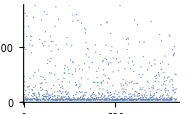

```mathematica
ListPlot[corredist]
```

```mathematica
Min[corredist]
```

147418.

```mathematica
Position[corredist,Min[corredist]]
```

{{698}}

```mathematica
correctlist = {};
For[i =1, i≤ 2001, ++i, 
ncorrect = 0;
For[j =1, j≤ 64, ++j,
p = pos[[i]].outcomeslast5mat[[j]];
(*Print[o = {p[[18]], outcomesmat[[j,18]],p[[18+32]], outcomesmat[[j,18+32]] }];*)
If[
Sign[outcomesmat[[j,18]]-outcomesmat[[j,32+18]]]== Sign[p[[18]]-p[[18+32]]],(*Print["correct"]*)ncorrect+=1(*Print["Incorrect"]*)
];
];
AppendTo[correctlist,ncorrect]
]
```

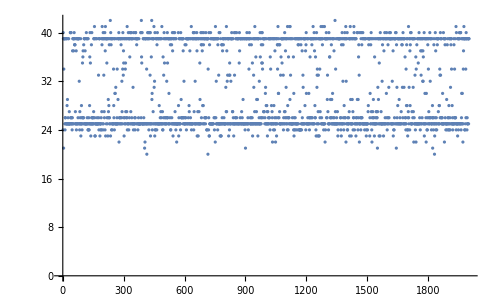

```mathematica
ListPlot[correctlist]
```

```mathematica
N[42/64]
```

0.65625

```mathematica
Max[correctlist]
```

42

```mathematica
Position[correctlist, Max[correctlist]]
```

{{234},{387},{438},{1341}}

```mathematica
MatrixForm[pos[[234]]]
```

(0.961018 | 0.0688589 | 0.0497457 | 0.0140335 | -0.0858235 | -0.0777497 | -0.0570781 | -0.0666796 | -0.00289431 | 0.0127667 | 0.0763217 | 0.0115962 | 0.0261924 | -0.013985 | -0.0761753 | -0.0340133 | 0.0649028 | -0.0640191 | 0.0216363 | -0.092761 | -0.0347831 | 0.073884 | 0.0780697 | -0.0855937 | 0.00783164 | 0.0783374 | 0.0447835 | 0.0779641 | 0.0381637 | -0.026015 | -0.0400768 | 0.0735316 | -0.0158157 | 0.0283238 | -0.082236 | -0.0206487 | 0.0643375 | 0.0178318 | -0.0927662 | 0.0179509 | 0.0287337 | -0.0862453 | 0.0914571 | -0.00989206 | 0.0428875 | -0.00540279 | 0.00040017 | -0.0742207 | 0.0581167 | -0.0847155 | 0.0470534 | -0.0254538 | -0.0620371 | -0.0415143 | 0.0306546 | -0.010384 | 0.0616241 | -0.0995483 | 0.0617791 | 0.00738301 | 0.0162184 | -0.093306 | 0.0945204 | 0.0526797
0.0128745 | 0.904032 | -0.0615369 | -0.0658341 | 0.0495933 | 0.0801113 | -0.0508717 | -0.0938823 | -0.0283329 | -0.061397 | 0.0854772 | -0.0977245 | -0.0783946 | 0.0511206 | 0.0234265 | 0.0782768 | -0.0279013 | 0.076252 | -0.0659489 | -0.00439947 | 0.00548446 | 0.0591852 | 0.00492909 | -0.0709465 | 0.0542214 | -0.0269553 | -0.0185534 | -0.017139 | -0.026901 | -0.0270262 | 0.0423481 | -0.0716398 | 0.0606814 | -0.0314554 | 0.0420802 | 0.0165138 | 0.00576725 | -0.0770394 | 0.0110593 | -0.0230484 | -0.0830812 | -0.0084953 | 0.053202 | 0.0970151 | 0.0265645 | 0.0440262 | 0.00690003 | 0.0277514 | -0.0521124 | -0.032434 | -0.0264526 | 0.0456671 | -0.0954588 | 0.0174737 | 0.0161376 | 0.0755861 | 0.0903421 | -0.0722737 | 0.0653042 | 0.00136329 | 0.0750672 | 0.0357726 | 0.0859131 | 0.0465595
-0.0232614 | 0.00685884 | 1.07575 | -0.0837046 | 0.0674669 | 0.083609 | -0.0620959 | -0.0751769 | 0.0790992 | -0.00170402 | -0.0544834 | 0.040309 | 0.0748138 | 0.0740696 | 0.00308345 | 0.0615573 | -0.0916469 | 0.077494 | -0.0919178 | -0.0703287 | 0.0533227 | 0.0694923 | -0.0432049 | 0.0909007 | -0.060822 | 0.0624773 | -0.097686 | -0.0408756 | 0.0162367 | 0.0980204 | -0.0056147 | -0.0973088 | -0.0464655 | -0.00484237 | -0.0492613 | 0.0964731 | -0.0395458 | -0.0114789 | 0.0235174 | -0.0726301 | -0.0916642 | -0.0245268 | 0.0135356 | 0.0151451 | -0.0286462 | 0.0973803 | 0.00464553 | -0.0505584 | -0.0808288 | -0.0597524 | -0.0913932 | 0.0648738 | -0.0527523 | -0.0998591 | 0.00347422 | 0.0282425 | -0.0321636 | -0.0974607 | -0.0902012 | -0.0419905 | -0.0388179 | 0.0262409 | -0.054515 | -0.0689398
0.0457777 | -0.0643447 | 0.0675836 | 1.08714 | -0.0642382 | 0.0802965 | 0.0599123 | 0.0438959 | 0.0627356 | 0.0938534 | 0.0342558 | 0.0139262 | 0.0588682 | -0.0166429 | 0.0644339 | -0.0467508 | -0.000156869 | 0.0863822 | 0.0356691 | -0.0853142 | -0.00769881 | -0.0668109 | 0.0859888 | -0.0873712 | 0.0558208 | 0.0000640095 | 0.00582313 | -0.0225465 | 0.0484248 | -0.0866417 | 0.0194722 | 0.0104193 | 0.0733938 | 0.0868554 | -0.0825647 | -0.0968294 | 0.0246128 | 0.0486429 | -0.0700814 | -0.06645 | 0.0581895 | 0.0778438 | -0.0289879 | 0.0473221 | 0.0371051 | -0.0877932 | 0.0576109 | 0.0699212 | -0.094773 | 0.0738865 | -0.0778667 | 0.0341755 | 0.0421816 | 0.0740779 | -0.0354323 | 0.0897084 | 0.00178749 | -0.0561843 | -0.00715144 | 0.0791838 | 0.0028469 | -0.0332533 | 0.0740378 | -0.0709936
0.0296043 | 0.0969072 | -0.0190961 | -0.0074 | 1.0249 | -0.0923524 | -0.00700098 | 0.0532123 | 0.0306704 | 0.0173332 | 0.0685619 | 0.0823564 | 0.0579958 | -0.0644864 | 0.0995297 | 0.0568536 | 0.0536316 | 0.0807437 | 0.0359614 | -0.0324569 | -0.0362287 | 0.077574 | 0.097104 | 0.0862352 | -0.0029804 | -0.00968518 | -0.00706851 | 0.0935626 | 0.0520107 | -0.033998 | 0.00524172 | 0.0526604 | -0.043675 | -0.0647524 | 0.0572337 | 0.0414417 | -0.0878975 | -0.0661415 | -0.0622606 | -0.00855562 | -0.0993125 | 0.0289943 | -0.080813 | -0.0719191 | -0.066051 | -0.0818024 | -0.00927326 | -0.0485925 | -0.0175742 | 0.0378833 | 0.0346765 | 0.0940324 | -0.00788192 | 0.0987338 | 0.0311696 | -0.0536146 | -0.0892446 | 0.00837348 | -0.00304647 | -0.0850302 | 0.0138844 | 0.00970826 | 0.00474699 | 0.0836173
0.0466168 | 0.0901847 | -0.00588383 | 0.0213257 | 0.0854141 | 1.01838 | 0.016742 | -0.0191057 | 0.00516563 | 0.00652023 | -0.0734056 | 0.0591811 | -0.0686044 | -0.0711674 | -0.0519151 | 0.035353 | 0.00266279 | 0.0804104 | -0.089622 | -0.00753731 | -0.00976338 | -0.00443546 | -0.0519178 | -0.009067 | -0.053614 | -0.00376142 | 0.0240974 | -0.0289354 | -0.0457275 | 0.0689574 | 0.0485366 | 0.0182831 | 0.0490825 | 0.00498433 | -0.0497418 | -0.00535531 | -0.0367359 | -0.000534623 | 0.0307578 | 0.0514868 | -0.0477697 | 0.0297375 | -0.0291823 | -0.0415033 | -0.0849949 | 0.0937667 | 0.0128916 | -0.0468258 | -0.064299 | -0.0202931 | 0.072457 | -0.00820894 | 0.071636 | 0.0548487 | -0.0440091 | -0.00302436 | -0.0586067 | -0.0569689 | -0.0678414 | -0.0359258 | -0.0237212 | 0.0252415 | -0.081675 | 0.0971258
-0.0259633 | -0.0512943 | 0.071251 | 0.0434273 | -0.0548544 | -0.0765745 | 1.09996 | 0.0190501 | 0.0549573 | 0.0694384 | -0.0578549 | 0.0797443 | 0.0527695 | 0.0735781 | 0.0510144 | -0.0817909 | -0.00637997 | -0.0957699 | -0.0818559 | 0.0185875 | -0.0639714 | 0.0396757 | -0.0390625 | -0.087747 | 0.0907555 | -0.0173886 | -0.0671196 | -0.0463053 | -0.0876723 | 0.0546627 | 0.018755 | -0.0226511 | 0.0806301 | -0.0130503 | -0.0680638 | -0.0984168 | 0.0254666 | 0.0460027 | 0.0338613 | -0.0790282 | -0.07087 | 0.0858977 | -0.0127932 | 0.0445173 | -0.0219054 | 0.00840589 | -0.076857 | -0.0572354 | -0.0472067 | 0.037317 | -0.0535567 | 0.0736532 | 0.0840056 | -0.0013408 | -0.00888581 | 0.0520277 | 0.0607458 | 0.0941552 | 0.0734434 | 0.0903064 | 0.00586204 | -0.031907 | -0.00899775 | -0.0964562
-0.0745053 | -0.0525087 | -0.0614613 | 0.0914649 | 0.0488615 | 0.0923975 | -0.0210311 | 1.0452 | 0.0022307 | -0.00417459 | -0.0266417 | -0.0107613 | -0.0736203 | 0.0978242 | 0.0264373 | -0.0122059 | -0.0801929 | -0.05442 | -0.0629026 | 0.0777753 | 0.02081 | 0.000428728 | -0.0102997 | -0.00521661 | -0.0374655 | -0.0676852 | -0.0600495 | -0.0779284 | 0.0308107 | 0.0354665 | -0.0690288 | 0.0400656 | 0.0360084 | -0.085055 | -0.0718668 | 0.0116382 | 0.0569971 | -0.0463661 | 0.0840908 | -0.0339018 | 0.0731694 | -0.0613149 | -0.0327455 | -0.0430908 | 0.0885392 | -0.0902181 | -0.0881224 | -0.0297617 | 0.0787587 | -0.0908692 | -0.0712349 | 0.0977863 | -0.0256556 | -0.0318332 | -0.0910762 | 0.00969921 | 0.0680181 | 0.0188658 | 0.0929905 | 0.0388497 | 0.0243593 | -0.0499268 | -0.0747694 | 0.0807189
-0.0557294 | -0.0950103 | -0.0883651 | -0.051566 | 0.0459677 | 0.037441 | -0.0134941 | 0.0569009 | 1.05672 | -0.0296272 | 0.0888999 | -0.0122707 | -0.091446 | 0.0131221 | -0.0920911 | 0.010901 | -0.0268878 | -0.0667341 | -0.0714353 | 0.0495292 | -0.0229123 | 0.000568022 | -0.0254228 | 0.0819942 | -0.0962384 | -0.0362912 | -0.00885684 | -0.0487049 | -0.0869742 | -0.0190561 | 0.0719615 | -0.09097 | 0.00197808 | 0.0868094 | -0.0645862 | -0.0154238 | 0.0284642 | 0.0788981 | -0.0897243 | -0.0550366 | 0.047706 | -0.0176043 | -0.0741239 | 0.098181 | -0.0365541 | 0.00557622 | -0.00208362 | -0.0728248 | 0.0714753 | 0.00315686 | -0.0951907 | -0.0315974 | -0.0319818 | -0.0620732 | 0.0963473 | -0.0831325 | 0.0735138 | -0.0617151 | 0.0842389 | 0.0685376 | 0.0682907 | 0.00052881 | 0.020384 | -0.0730611
-0.0598464 | -0.0233199 | 0.0257647 | -0.0540746 | -0.0205802 | -0.073762 | 0.0950653 | -0.0792225 | 0.0404467 | 0.999407 | -0.0226119 | 0.0987212 | -0.0430857 | 0.00901237 | 0.0220739 | 0.0632031 | 0.0479927 | 0.0235241 | -0.0398231 | 0.0679247 | 0.0217119 | -0.0291892 | -0.0419007 | -0.069319 | 0.0464063 | -0.0543144 | -0.0321946 | -0.0934667 | -0.00141312 | 0.0575413 | 0.0213401 | 0.0658893 | -0.0734236 | -0.00750515 | 0.0100311 | -0.0325094 | 0.0948141 | 0.0370695 | -0.0514681 | 0.0134913 | 0.0685978 | -0.0046487 | -0.0189259 | 0.0362538 | 0.0509574 | -0.00197928 | 0.0610206 | -0.0175679 | 0.06699 | -0.0300157 | -0.0366828 | -0.0124575 | 0.0969181 | -0.0364793 | -0.0479209 | -0.0392749 | 0.0894144 | -0.0463237 | 0.0428996 | 0.0589352 | 0.0438745 | -0.0869589 | 0.0230007 | 0.0311463
0.0377773 | 0.0911119 | -0.0754635 | -0.0991975 | 0.0806319 | 0.0118928 | 0.0894483 | -0.0628169 | 0.00797719 | 0.0313365 | 1.07478 | -0.006608 | -0.0132355 | -0.0175052 | 0.0268007 | -0.00974677 | 0.062061 | 0.0296464 | -0.0892681 | 0.0103223 | 0.0291844 | 0.0115487 | -0.0719465 | -0.087693 | -0.0581889 | -0.00212763 | -0.0706774 | -0.0594143 | 0.0712961 | -0.0251227 | 0.0659998 | -0.0988926 | 0.0409474 | 0.092643 | 0.0510536 | 0.091547 | 0.0836313 | 0.050046 | -0.0606839 | 0.0573447 | 0.0907611 | 0.0961244 | -0.0256547 | 0.0354299 | -0.0926744 | 0.00907922 | 0.00293258 | 0.0429635 | 0.0552375 | -0.0945109 | 0.0111074 | 0.0911765 | -0.026427 | 0.0890431 | -0.00978193 | -0.0840886 | -0.045795 | -0.0895827 | -0.037842 | 0.0116953 | 0.021624 | 0.000990008 | 0.0475162 | -0.0702949
-0.0907713 | -0.00985936 | -0.0369319 | 0.0766744 | 0.0567973 | 0.0708992 | 0.0718526 | 0.093437 | 0.0643936 | 0.0394909 | -0.0347212 | 1.02618 | 0.054797 | -0.0184578 | 0.0596667 | 0.0661487 | 0.0690121 | -0.0908727 | 0.0587423 | 0.00544089 | 0.0561872 | 0.0185799 | 0.0780642 | -0.0568326 | -0.0358804 | -0.0950004 | 0.0683101 | 0.00940779 | -0.0316938 | -0.0403733 | -0.0164608 | 0.00906998 | -0.0913733 | 0.0734929 | 0.0737133 | 0.0903361 | 0.0797238 | -0.081763 | 0.01312 | 0.0209999 | -0.0463415 | -0.0360474 | -0.030468 | 0.0769031 | 0.0244877 | -0.0355394 | -0.0375549 | 0.037926 | 0.0826266 | 0.0691407 | -0.0969411 | -0.0475036 | -0.0842661 | -0.00987911 | -0.0654457 | -0.0481695 | -0.0419475 | 0.00296191 | 0.0985608 | -0.0699486 | -0.0287135 | -0.0877685 | 0.0421478 | -0.0915413
-0.0300674 | 0.0492803 | 0.0549012 | -0.0949179 | -0.0526162 | -0.0390486 | -0.00879577 | -0.096089 | -0.0638745 | 0.0405439 | -0.0241671 | 0.00988215 | 1.01636 | -0.0162003 | 0.0880733 | -0.00554472 | 0.00430764 | 0.0629948 | 0.0885598 | -0.068821 | -0.00876084 | 0.0397562 | 0.050153 | -0.00926507 | 0.0825987 | -0.057125 | 0.0280176 | 0.0261637 | -0.0858693 | -0.0961593 | -0.0721876 | -0.0202006 | 0.0300899 | -0.049606 | 0.0713973 | -0.0512934 | -0.0177605 | -0.042869 | 0.0634266 | -0.0217548 | -0.0384283 | -0.0945037 | 0.00217699 | -0.0726032 | -0.0542435 | -0.0695083 | 0.06162 | -0.0682558 | 0.00282486 | 0.0903631 | 0.0161135 | 0.0103881 | 0.0655225 | 0.0220383 | -0.0454483 | 0.0747421 | -0.0987986 | -0.0313071 | -0.0995203 | -0.0614169 | -0.052291 | -0.0871171 | -0.0617405 | 0.0861759
0.07091 | -0.0581091 | 0.095267 | 0.0162066 | 0.0855376 | 0.079944 | -0.040081 | 0.00145486 | -0.0574737 | 0.0697087 | -0.0527034 | -0.0604943 | -0.089362 | 1.0744 | -0.0644432 | -0.00354829 | 0.0364077 | -0.0196537 | -0.0753734 | -0.0593117 | 0.0924906 | -0.000164385 | 0.0735962 | 0.0874567 | -0.0873341 | -0.00234904 | -0.0848963 | 0.0297564 | -0.0841506 | 0.0776055 | -0.0537924 | -0.0673362 | 0.00328921 | -0.0149476 | -0.0955271 | -0.00083949 | 0.0310287 | -0.00825778 | -0.0244715 | -0.0784202 | 0.0878232 | 0.00309818 | -0.0468285 | 0.0277613 | -0.0690194 | 0.0832965 | -0.0443809 | -0.0114565 | 0.0254684 | -0.011157 | -0.0902025 | 0.0228534 | 0.0271357 | -0.0292071 | 0.00635188 | -0.00706059 | 0.0962463 | 0.0765482 | 0.0245115 | 0.0306134 | 0.0579553 | 0.0931238 | -0.0391107 | -0.0175454
-0.00743669 | 0.0201838 | 0.0380727 | -0.0734398 | -0.0809219 | 0.0273845 | -0.0970053 | 0.0486855 | -0.0593558 | 0.0999941 | -0.0867995 | -0.00734506 | 0.0202738 | 0.041599 | 1.02133 | -0.0222569 | -0.0131512 | -0.0477885 | -0.0467611 | -0.0639795 | 0.0694586 | -0.0188214 | -0.0949925 | -0.0382752 | -0.0135012 | 0.0937521 | 0.0323154 | 0.0333875 | 0.0124816 | 0.0542262 | 0.0980575 | 0.0927104 | 0.0485778 | 0.0783568 | 0.034568 | 0.0795112 | -0.0184336 | 0.0929758 | -0.0354882 | 0.0684777 | -0.0649007 | -0.00975372 | 0.0899715 | 0.0708305 | 0.0911251 | -0.0208035 | 0.0852987 | -0.0375479 | -0.0417055 | -0.0765893 | 0.0904651 | -0.0121021 | -0.0798736 | 0.048939 | -0.0562788 | 0.0910575 | -0.0983536 | 0.0441233 | 0.0157009 | -0.0997963 | -0.0564904 | -0.0824276 | 0.0680324 | -0.0274456
0.0748162 | 0.0959343 | -0.0535665 | -0.0740063 | 0.0927331 | 0.0483629 | -0.0914965 | 0.00803204 | -0.0516997 | 0.080811 | 0.0652054 | -0.0205668 | -0.0265629 | 0.0653781 | -0.0170899 | 0.91396 | 0.0652833 | 0.0131607 | -0.0470543 | 0.0495592 | -0.070438 | -0.0794288 | -0.00278099 | -0.014724 | 0.0222816 | -0.0213258 | 0.0199029 | -0.00537407 | 0.0830917 | 0.0890591 | -0.093657 | 0.00675896 | 0.0742175 | 0.0647963 | -0.0226797 | 0.075487 | 0.0591558 | 0.0947107 | 0.0761453 | -0.0684823 | 0.0937713 | -0.0567144 | 0.0989898 | -0.0577301 | 0.0670832 | -0.0118837 | -0.045694 | 0.0791096 | -0.0375351 | -0.0934879 | -0.0538802 | -0.0744697 | -0.0967295 | 0.0600095 | -0.00147527 | 0.0652287 | -0.0144173 | -0.0214348 | 0.0464343 | -0.0481159 | -0.0785855 | -0.0162459 | -0.000581248 | -0.0920448
-0.0855699 | -0.0527196 | 0.0867142 | -0.0956449 | -0.0329694 | 0.0839473 | -0.0456676 | 0.0082404 | 0.0131196 | 0.0146263 | 0.0343279 | 0.0814168 | -0.087717 | -0.00165285 | 0.078029 | 0.0398258 | 0.969607 | -0.0638296 | 0.0508277 | -0.00699262 | -0.0587075 | 0.0584782 | -0.0713034 | -0.0713722 | -0.0670006 | -0.0861897 | -0.0301993 | 0.0121128 | 0.033422 | -0.0275834 | -0.0572432 | -0.00132 | 0.0371897 | -0.0414622 | 0.0956921 | 0.0920067 | -0.0491317 | 0.0594968 | -0.0611581 | -0.0522868 | -0.00144006 | -0.0303889 | 0.0306802 | 0.00985912 | -0.079036 | 0.0855007 | -0.0796204 | 0.094526 | -0.0321417 | 0.0115482 | -0.0912481 | 0.0168186 | -0.0232774 | -0.0286374 | -0.0177709 | 0.0787942 | -0.0453454 | -0.00620561 | 0.0830551 | 0.0829105 | -0.000333312 | -0.0722449 | 0.0370443 | -0.0601314
-0.0673142 | 0.0847271 | 0.0591414 | -0.0828383 | 0.00762542 | -0.0671722 | -0.0168358 | 0.028408 | 0.0936925 | 0.083304 | 0.0989893 | -0.00271965 | -0.0730102 | -0.0821112 | -0.0136988 | 0.0995462 | 0.0590348 | 0.988567 | -0.0270102 | -0.0497078 | 0.0593296 | -0.00658405 | -0.0408029 | 0.00805284 | 0.0767615 | 0.000959502 | 0.0290548 | -0.0345473 | 0.00825839 | -0.0382019 | -0.0798492 | -0.00975059 | 0.0620225 | 0.0793462 | -0.0719049 | 0.0853132 | 0.0241488 | 0.0401163 | -0.0940364 | -0.0374648 | 0.0555723 | 0.0135146 | 0.0388813 | -0.0747535 | 0.0202511 | -0.00119883 | -0.0778783 | 0.070411 | 0.0509129 | 0.0838437 | 0.0532229 | -0.0944641 | -0.033432 | 0.0801978 | 0.0714517 | 0.00289343 | -0.0174047 | 0.0457185 | -0.0808259 | 0.0417157 | 0.048401 | 0.0893362 | 0.0620514 | -0.038464
0.0569172 | 0.0408517 | -0.0756653 | 0.0396042 | 0.0832741 | -0.00697766 | 0.0961788 | 0.0234752 | 0.0453645 | 0.0656415 | 0.0395278 | -0.0000836408 | 0.0708132 | -0.0589392 | 0.0729539 | 0.0842092 | -0.0917234 | -0.0435979 | 0.973233 | 0.0782734 | -0.0769251 | -0.0331327 | -0.0854708 | 0.0802397 | 0.0692791 | -0.0120496 | 0.0627961 | -0.0146481 | 0.0758584 | -0.0875535 | -0.0438999 | 0.0931718 | 0.000406607 | -0.0118214 | -0.0062309 | 0.0857231 | 0.0665716 | -0.0784372 | -0.0946689 | -0.0604264 | -0.0707227 | -0.0619588 | -0.0492239 | -0.0745938 | -0.0500561 | 0.0925912 | -0.0380692 | 0.0956666 | 0.0107521 | -0.079482 | -0.0416099 | -0.0852946 | -0.0168646 | 0.00364036 | 0.0782999 | 0.0375265 | 0.0632808 | 0.0989619 | -0.0808478 | -0.076427 | 0.0582096 | -0.0641148 | -0.074794 | 0.0940648
0.0247711 | -0.0576054 | -0.00232377 | 0.0773756 | -0.0894857 | 0.0697305 | 0.0600214 | -0.00488269 | -0.0321085 | -0.0708547 | -0.0811599 | -0.0602491 | 0.0807188 | -0.0251482 | -0.0569652 | -0.0613063 | -0.0516517 | 0.0915488 | 0.0285843 | 0.949749 | -0.0352703 | 0.00163488 | -0.0904072 | -0.0246702 | 0.0235031 | 0.0261635 | 0.0706527 | 0.0264143 | -0.00634723 | -0.0860614 | 0.0604214 | 0.0445643 | -0.00979776 | 0.0320992 | -0.083633 | 0.0772055 | 0.0442979 | -0.0609255 | -0.0603243 | 0.00606758 | -0.0362597 | 0.0068775 | 0.061958 | -0.00239283 | 0.0402536 | 0.0513996 | -0.041769 | 0.0666412 | 0.0605785 | 0.0822199 | 0.0987234 | 0.0621895 | 0.0937954 | 0.0871196 | -0.0699707 | 0.0400264 | -0.0819899 | 0.0789208 | 0.00450981 | -0.0429712 | 0.0420499 | -0.0013945 | 0.00927327 | -0.0274164
-0.00060702 | -0.022709 | -0.0881182 | -0.0419283 | -0.0289717 | -0.00369921 | 0.0181896 | -0.0962467 | 0.0176404 | 0.0152982 | -0.0174691 | -0.0150855 | -0.0102817 | -0.0215275 | 0.0346918 | 0.0926721 | 0.0975897 | 0.0102152 | -0.00140775 | -0.0465869 | 0.935953 | 0.014563 | 0.0024496 | -0.0571542 | -0.0420489 | 0.0473527 | 0.0540479 | 0.00122595 | -0.0775616 | -0.0839819 | 0.0579218 | 0.0394805 | -0.00116944 | -0.0476741 | 0.0333754 | 0.0392611 | -0.045368 | -0.0910174 | -0.0383885 | 0.0817773 | 0.0938381 | 0.0599014 | -0.021105 | 0.0664938 | 0.0153892 | -0.0108832 | -0.08256 | 0.0104268 | -0.0892878 | 0.00698136 | 0.00162427 | -0.0866315 | 0.0697296 | -0.0255296 | -0.0773433 | 0.0193766 | 0.0912516 | -0.0985503 | 0.044352 | -0.0588052 | -0.0645999 | 0.0081039 | -0.0507231 | -0.0894374
-0.00311444 | 0.0585805 | -0.0688838 | 0.0371454 | 0.00219862 | -0.0656568 | 0.0615474 | -0.051578 | 0.0259153 | 0.0617157 | -0.0677088 | 0.0868028 | -0.099122 | 0.00878534 | 0.012221 | 0.0772727 | 0.0511904 | 0.0689909 | 0.00160909 | -0.0419032 | -0.059892 | 0.929231 | 0.049718 | -0.01662 | 0.0375254 | 0.0894282 | -0.00513391 | -0.06488 | 0.096773 | -0.0944386 | -0.0731088 | 0.0430278 | -0.0381626 | -0.0152035 | 0.0380372 | -0.072337 | 0.0643652 | -0.0453915 | -0.0404449 | 0.0957527 | 0.0478145 | -0.0342877 | 0.0163846 | -0.0433843 | -0.0825404 | -0.0798201 | -0.0190657 | -0.0130917 | 0.0229543 | -0.00680607 | 0.0608 | -0.0749901 | 0.0714271 | -0.0624808 | -0.0732385 | 0.0529262 | 0.0487096 | 0.0530715 | -0.0566939 | -0.00231509 | -0.067602 | 0.0689139 | -0.00596925 | -0.0370353
0.0276919 | -0.0277286 | -0.0272287 | -0.0751632 | 0.00947241 | 0.0989625 | 0.0331667 | 0.0297011 | -0.0367392 | -0.00171618 | -0.0122248 | -0.00532127 | -0.00954877 | 0.021162 | 0.0762801 | 0.0739801 | -0.0954586 | -0.0423359 | -0.0623961 | 0.054052 | -0.0994757 | 0.0915047 | 1.00787 | 0.00205986 | -0.0312866 | 0.00251452 | -0.0632695 | -0.0383457 | 0.0281961 | -0.0626909 | -0.0682346 | 0.0269295 | 0.0395381 | 0.0392712 | -0.0919706 | -0.0124079 | -0.0497135 | -0.0811989 | 0.0917427 | 0.0367443 | 0.0261049 | 0.0400735 | -0.0158225 | 0.0312567 | 0.0319518 | 0.0700056 | -0.044318 | -0.0408588 | -0.0826982 | 0.051398 | -0.0326377 | -0.0988191 | -0.0383087 | -0.0777854 | 0.0381884 | 0.075565 | -0.0475083 | -0.0859664 | -0.0110018 | 0.010475 | 0.0446229 | -0.0467333 | -0.00173421 | -0.0735393
0.00443647 | -0.0210345 | -0.0441869 | -0.0424662 | -0.0432238 | 0.0244801 | -0.00715221 | 0.0674891 | -0.0365715 | -0.00126687 | -0.0192365 | -0.0464357 | 0.0108718 | 0.0935746 | -0.0973117 | -0.0617871 | -0.0858704 | -0.0469853 | 0.0983289 | 0.0534219 | 0.00514378 | -0.0672902 | 0.052425 | 1.00274 | -0.047166 | -0.0554563 | 0.0203163 | 0.0077769 | 0.0677147 | -0.00233751 | 0.0382157 | 0.0485736 | -0.0826109 | 0.0535869 | 0.0237382 | 0.0845802 | -0.030575 | -0.0446394 | -0.0447579 | -0.0152705 | -0.00936505 | -0.021769 | -0.0541283 | 0.090364 | 0.0124089 | -0.0937098 | -0.0198148 | 0.0161225 | -0.0532794 | -0.046037 | 0.00456283 | -0.0483068 | 0.0913588 | -0.096465 | -0.0310679 | 0.0851965 | 0.0896236 | 0.0778808 | 0.0364518 | 0.0768225 | -0.00495053 | 0.0883951 | -0.067386 | 0.0702364
0.0690744 | -0.00167882 | 0.0734572 | 0.0165545 | 0.0931468 | -0.00954559 | 0.0544071 | -0.0249798 | 0.0437941 | -0.0736488 | 0.084499 | 0.0128334 | -0.0741842 | -0.0790687 | -0.0582451 | 0.0990668 | -0.0563727 | 0.0327811 | 0.0628704 | 0.00473833 | -0.0264741 | -0.0311022 | 0.0262459 | -0.0183105 | 0.905897 | 0.0984155 | -0.0154397 | 0.0386602 | 0.0163664 | -0.0654122 | -0.0550726 | -0.0964279 | 0.0961803 | 0.0753324 | -0.0515252 | 0.0406663 | -0.0749908 | 0.0501156 | 0.0117284 | 0.0584586 | 0.0570206 | 0.0586096 | 0.0438915 | -0.0275493 | -0.0963256 | 0.0779237 | -0.0474013 | 0.022519 | -0.0572067 | 0.0158388 | -0.0629172 | 0.0237726 | -0.0685272 | -0.0336075 | -0.00181476 | -0.0183321 | -0.0125172 | 0.0740022 | 0.048588 | 0.0725826 | -0.0136232 | 0.0779038 | 0.0726113 | 0.0300186
0.0488978 | -0.0516524 | 0.0228904 | 0.0830704 | -0.0850231 | -0.0956727 | 0.0433827 | 0.0559006 | -0.0928329 | -0.0569308 | 0.0261955 | 0.0356698 | -0.0460601 | 0.0233488 | 0.0357044 | -0.0218541 | -0.092461 | 0.0955525 | -0.0285157 | 0.0985764 | 0.00924716 | 0.0402287 | -0.0916061 | 0.0288069 | -0.0596553 | 1.0811 | 0.0534547 | 0.0923374 | 0.027712 | 0.00915403 | 0.011684 | 0.0213574 | -0.0971766 | 0.0878651 | -0.0687211 | -0.021951 | -0.065412 | 0.0413054 | -0.0949005 | -0.0089664 | -0.0862771 | -0.0835713 | 0.00854368 | 0.090162 | 0.0424329 | 0.0242207 | 0.0818294 | 0.0620364 | 0.0701979 | 0.0752409 | -0.0308852 | 0.0424308 | 0.00258491 | 0.0188827 | 0.0199376 | 0.00222758 | 0.0740489 | 0.0879532 | -0.0539183 | 0.0462096 | 0.0766019 | -0.03583 | -0.00258267 | 0.00718033
-0.0557628 | 0.0598438 | 0.000952595 | 0.0498821 | -0.00880158 | -0.0410608 | -0.00125925 | 0.0804956 | 0.0804078 | 0.0206344 | -0.0516482 | -0.0622794 | -0.0469105 | -0.0261982 | -0.0563885 | 0.0248744 | -0.0465074 | 0.016062 | -0.0845104 | -0.0149679 | -0.0367248 | 0.0775673 | 0.0880883 | -0.0934699 | -0.0343123 | 0.026776 | 0.909741 | -0.0424531 | 0.0973505 | 0.0319804 | 0.0980562 | 0.038656 | -0.0493443 | 0.0191992 | 0.0835189 | 0.016588 | -0.070159 | 0.0925084 | -0.0369251 | 0.0477468 | -0.0548798 | 0.00598908 | -0.0567908 | -0.0884915 | 0.0427129 | -0.00775672 | 0.0824342 | 0.0493958 | -0.0904818 | 0.0272842 | 0.0519381 | 0.00982721 | 0.0632073 | -0.0969445 | -0.0584259 | 0.00453925 | 0.0975784 | 0.052534 | -0.0829961 | 0.0645245 | -0.0615008 | -0.0933004 | -0.0400844 | -0.00106315
0.0895476 | -0.069185 | 0.00489407 | 0.0615733 | 0.0711023 | -0.0427109 | 0.0152191 | -0.0664163 | -0.0957286 | -0.0906266 | 0.0682309 | 0.0328118 | 0.025649 | -0.0377174 | 0.0457707 | -0.0557228 | 0.052813 | -0.0286762 | 0.00918455 | 0.0160803 | 0.00572724 | -0.00528894 | -0.0655887 | 0.000221552 | 0.0884226 | 0.00633753 | -0.0224848 | 1.09261 | -0.0744214 | -0.00135189 | 0.0417023 | -0.00779409 | -0.0934136 | 0.0586306 | 0.0522712 | 0.001746 | 0.0332551 | 0.0910148 | -0.0455508 | -0.0093048 | 0.0599694 | -0.00167872 | 0.0964351 | -0.0274579 | -0.093019 | -0.0540186 | -0.0201683 | 0.0491979 | 0.00417831 | 0.0992237 | -0.0884468 | 0.0659494 | 0.0501107 | 0.063856 | 0.0710469 | 0.0402761 | -0.00809542 | 0.0188836 | 0.0218039 | 0.0914155 | 0.0441348 | 0.0316939 | 0.0120678 | 0.011906
0.0284977 | 0.0316578 | 0.062379 | 0.079191 | -0.0430675 | 0.0625519 | 0.0815903 | 0.0623607 | -0.00487109 | 0.0845651 | 0.0609959 | 0.00344736 | 0.0979192 | -0.0894619 | 0.0520909 | -0.0824734 | -0.0769678 | 0.0179943 | -0.0996054 | -0.0589674 | 0.0861107 | -0.0832201 | 0.0129644 | 0.0696694 | 0.0240578 | -0.0748565 | 0.0248626 | -0.0541621 | 0.942765 | -0.0861767 | -0.0311971 | -0.0459543 | -0.0985131 | 0.0709951 | -0.0504514 | 0.0865773 | 0.023724 | -0.0441128 | -0.0105695 | -0.0431079 | 0.0710281 | -0.0782963 | -0.0172682 | 0.0711244 | 0.078057 | -0.0049848 | 0.0100239 | -0.00863512 | 0.0164008 | 0.0433408 | -0.0745265 | -0.0331738 | -0.0308498 | -0.00582045 | -0.00450057 | 0.0204924 | -0.00600958 | -0.03466 | -0.0286854 | -0.0929907 | 0.0591414 | -0.0947295 | -0.08085 | -0.0226418
-0.0209592 | -0.00246306 | 0.0778952 | -0.0642207 | -0.0139033 | -0.000592205 | -0.0577817 | -0.0996577 | 0.0442128 | 0.0463176 | 0.0741652 | 0.0694151 | -0.0921444 | 0.053607 | 0.0433147 | 0.032318 | -0.0605744 | 0.0539072 | 0.0782224 | 0.0691217 | -0.0970798 | -0.074519 | -0.0826743 | 0.00813868 | -0.0205467 | 0.0121281 | 0.00739342 | 0.0643802 | -0.0341669 | 0.951719 | -0.0908465 | -0.0552457 | 0.0887514 | -0.019882 | -0.0329562 | -0.0763872 | 0.00798654 | -0.0640784 | -0.0551832 | -0.036552 | -0.0832698 | 0.0213345 | 0.0865127 | 0.00955436 | -0.0976871 | -0.087209 | 0.0479656 | -0.0904362 | 0.0327333 | 0.0791349 | 0.00305279 | 0.0798864 | -0.0511484 | -0.0390395 | -0.081145 | -0.0384005 | -0.0770638 | -0.0794876 | -0.0574857 | 0.0475387 | 0.00385409 | -0.0824085 | 0.0180843 | 0.0486026
-0.0790296 | -0.06601 | 0.0949746 | -0.045425 | -0.0970666 | 0.0112382 | -0.0210059 | -0.0628475 | -0.0743806 | 0.0528632 | 0.0493549 | 0.0731978 | -0.0862116 | 0.00361307 | 0.0145433 | -0.0566883 | -0.01227 | 0.0200679 | 0.0298195 | -0.0476543 | 0.0265076 | -0.00904727 | 0.0198397 | -0.0204574 | -0.00166045 | 0.00211729 | 0.0617851 | -0.0813675 | 0.0202653 | 0.0518424 | 0.929464 | -0.0397361 | 0.0712017 | -0.0259717 | -0.0686215 | -0.090838 | 0.0429964 | 0.0515496 | 0.0314354 | 0.0201038 | -0.0604007 | 0.0074112 | 0.0449975 | -0.0451529 | -0.023602 | 0.0295897 | -0.0991584 | 0.021446 | 0.0298651 | 0.0341361 | 0.0503045 | 0.0296055 | -0.00993347 | -0.0872432 | 0.0452131 | 0.0113864 | -0.0903303 | -0.0556793 | 0.0559741 | -0.0920002 | -0.0477822 | 0.0540035 | -0.048182 | -0.0914081
-0.0516484 | 0.0274695 | -0.0609192 | 0.0358738 | 0.0116348 | -0.0709894 | -0.0390819 | 0.0588324 | 0.0756999 | 0.00138862 | 0.0486233 | -0.0120774 | 0.00558675 | -0.0819355 | 0.0382512 | -0.0346989 | -0.0718357 | 0.033043 | 0.0763585 | -0.0100642 | 0.078401 | -0.0158275 | -0.00175263 | -0.0324314 | -0.0511521 | 0.00131896 | 0.0165905 | -0.0451359 | -0.0912977 | 0.0649404 | -0.00674258 | 0.980289 | 0.0930016 | -0.0563611 | 0.00919485 | 0.0732333 | 0.096216 | -0.0991787 | -0.0630054 | -0.0445697 | -0.0895395 | 0.0182222 | 0.0442968 | -0.0480643 | 0.0621981 | -0.00505118 | -0.00276336 | 0.0979152 | -0.0936102 | 0.0196728 | 0.0246011 | -0.0245202 | -0.0758772 | -0.0998203 | 0.0655123 | -0.00612057 | 0.0186514 | 0.0895626 | 0.0999381 | 0.0357605 | -0.070901 | -0.0956202 | 0.0244982 | 0.0263245
0.0655257 | -0.0457942 | -0.000951107 | -0.00589172 | 0.0308048 | -0.0128465 | -0.0100131 | -0.0618977 | 0.0780986 | -0.0781995 | 0.0902094 | -0.00871948 | -0.0787478 | -0.0849216 | 0.0270165 | -0.0840731 | 0.00620505 | 0.0695163 | 0.0289009 | -0.0443891 | -0.0291242 | -0.00825954 | 0.0863562 | -0.0159048 | 0.0798696 | -0.07071 | -0.0130896 | 0.0619383 | 0.0393727 | -0.064928 | 0.0232367 | -0.0905739 | 0.955496 | -0.0769224 | -0.0953985 | 0.0120955 | 0.0271312 | 0.00718824 | 0.0360843 | -0.0894815 | -0.0522383 | 0.0518014 | -0.0627115 | -0.0426604 | 0.072563 | -0.0691977 | -0.0494016 | -0.0126345 | 0.0310898 | 0.0627729 | 0.00211475 | 0.017743 | -0.0529461 | 0.0229993 | -0.0835815 | 0.0818782 | -0.0551822 | 0.0392323 | -0.0981678 | 0.0863849 | -0.0994077 | 0.0075964 | -0.0530434 | -0.062945
0.026149 | -0.0741208 | -0.00808449 | 0.00414021 | 0.0998299 | -0.00135506 | -0.0000212578 | -0.051132 | 0.0438789 | 0.0826878 | 0.0709205 | 0.0183901 | 0.0714167 | -0.00114025 | 0.00409257 | 0.016423 | -0.0730243 | -0.0471949 | -0.0418521 | -0.0379177 | -0.0149752 | -0.0353876 | 0.0368658 | 0.0229849 | 0.0548182 | -0.0561088 | -0.0397224 | 0.0866546 | 0.0255235 | 0.00322884 | 0.00559869 | -0.0975227 | 0.015463 | 1.06191 | 0.0303203 | 0.057733 | -0.00185291 | 0.00507714 | 0.0714184 | -0.0808226 | 0.0863335 | -0.0818611 | 0.0379195 | -0.0735769 | 0.0682549 | 0.0414293 | 0.0282111 | -0.0913693 | -0.0295548 | 0.092375 | -0.0778198 | -0.0958034 | 0.0814202 | 0.0671014 | -0.0836081 | -0.0020433 | -0.0635079 | 0.0194322 | -0.0553675 | -0.0959957 | -0.0717555 | -0.0260137 | -0.0729772 | -0.0300642
-0.0263306 | -0.0639374 | 0.0000684458 | -0.0697105 | -0.0504063 | -0.00735662 | 0.0285764 | -0.0421763 | 0.00375275 | -0.0209659 | -0.0811958 | -0.0616123 | 0.056331 | -0.0566239 | -0.0279982 | -0.0517158 | -0.0391246 | -0.0112103 | 0.0287413 | 0.024439 | 0.0452181 | -0.0884638 | -0.0701831 | -0.0461778 | 0.0476537 | -0.0459667 | -0.0615062 | -0.0705601 | -0.0324677 | -0.0135061 | 0.0407998 | -0.0945983 | 0.0206672 | -0.0525946 | 1.09968 | -0.0769001 | 0.0238879 | 0.00735919 | 0.0193399 | 0.0741368 | -0.0475911 | 0.017731 | -0.0302381 | -0.004352 | -0.00118204 | -0.0922245 | 0.060831 | -0.0672202 | 0.0600026 | -0.0610522 | 0.0875036 | 0.0749848 | 0.0382696 | -0.0692119 | -0.0589742 | 0.040533 | 0.0532258 | -0.0144157 | 0.0601584 | -0.0682796 | 0.000206077 | -0.0599761 | -0.00085617 | -0.0862237
-0.0985806 | 0.0404483 | 0.0300363 | -0.0974364 | -0.0114063 | -0.0101798 | 0.00175775 | 0.0489509 | 0.0269394 | -0.0932362 | 0.0420511 | 0.0674839 | 0.0872047 | 0.0404147 | 0.0767598 | 0.086314 | 0.0661185 | -0.00826299 | -0.0552014 | 0.0924447 | -0.0880423 | -0.00405637 | 0.0785526 | 0.0321778 | 0.0382362 | 0.00350358 | -0.0848957 | 0.0646266 | 0.0849099 | -0.0391717 | -0.0697006 | -0.029614 | 0.0348445 | -0.0718541 | 0.0988703 | 0.996876 | 0.0398283 | 0.0286528 | -0.0961137 | 0.0209225 | 0.0104411 | -0.0944623 | 0.00293503 | -0.0243103 | 0.0948797 | -0.0300938 | 0.00462354 | -0.0304875 | 0.0580969 | -0.0739299 | -0.0618887 | -0.034293 | 0.0449154 | 0.0762762 | -0.0627593 | -0.0901438 | -0.026834 | -0.0494816 | 0.0802682 | 0.0269701 | -0.0284506 | 0.0623775 | 0.0466758 | -0.0722694
0.0565156 | 0.0678355 | -0.0987543 | -0.039697 | -0.0383066 | -0.000268145 | -0.0153175 | -0.0713138 | -0.0457384 | -0.0840551 | 0.00147989 | 0.0605742 | -0.0539431 | 0.0528732 | 0.00445619 | -0.0333003 | -0.0411502 | -0.04187 | -0.0620794 | 0.0313278 | 0.0706052 | -0.0203881 | 0.00902816 | 0.0681443 | 0.016954 | -0.00884431 | -0.0772194 | 0.0396812 | 0.0636004 | -0.0196051 | 0.0673569 | -0.0932689 | 0.0542412 | 0.0484255 | -0.0863636 | -0.0756191 | 0.904047 | 0.0518315 | -0.093337 | 0.0172005 | -0.0130236 | -0.00254733 | -0.00728056 | 0.0504672 | -0.0765407 | 0.0668438 | -0.0627725 | -0.0999655 | 0.0410609 | 0.0260991 | 0.0799256 | 0.0569538 | -0.0720493 | -0.0316764 | -0.0889877 | -0.0211275 | -0.00809027 | -0.0572203 | 0.0239428 | -0.0282702 | -0.0701994 | -0.0724389 | 0.0652582 | -0.0846121
-0.0306178 | -0.0376652 | 0.0488142 | -0.0326313 | -0.0119169 | -0.0790265 | 0.00229065 | -0.0365921 | -0.058503 | 0.0621816 | -0.00744719 | -0.0355147 | -0.0724169 | 0.0984311 | -0.0988732 | -0.0505709 | 0.0610484 | 0.0765775 | 0.0867569 | 0.0911794 | -0.0590963 | -0.0318903 | 0.0756098 | 0.08979 | -0.0200762 | 0.087293 | 0.0451339 | -0.00683767 | -0.0423281 | 0.0334496 | 0.0142191 | -0.0945337 | -0.0709273 | 0.0965253 | 0.00619709 | 0.0186228 | 0.0580225 | 1.03575 | 0.0891517 | -0.0693355 | -0.0742988 | 0.0422051 | 0.0536399 | -0.05383 | 0.0805832 | 0.0586533 | -0.0915571 | -0.0678543 | 0.0333805 | 0.0924522 | -0.0824807 | -0.0447786 | -0.0283692 | 0.0495778 | -0.0744228 | 0.0149502 | 0.0860781 | -0.00135411 | -0.0902422 | 0.0236545 | -0.00527676 | 0.0929155 | -0.0318397 | 0.0520855
-0.0893452 | -0.0379572 | -0.075033 | -0.0632093 | 0.0596451 | -0.0548879 | -0.0644022 | 0.0970145 | 0.082369 | 0.0479724 | -0.0230591 | 0.0343038 | 0.00394753 | 0.0244047 | 0.00767709 | -0.0210449 | -0.0298816 | 0.0961106 | 0.078969 | 0.0446347 | 0.0839509 | -0.025463 | 0.0458011 | -0.0248225 | 0.072898 | 0.0449152 | -0.0420886 | -0.0321252 | 0.00659974 | -0.0284159 | 0.072402 | -0.0929791 | -0.0919858 | 0.095131 | 0.0165069 | 0.0406663 | 0.0537275 | 0.076956 | 1.00309 | 0.0295961 | -0.0517339 | 0.0707241 | -0.0853149 | 0.0540429 | 0.0583919 | 0.0873129 | 0.00854518 | -0.0485058 | -0.000385053 | -0.0707645 | -0.0682566 | -0.0146978 | 0.00540851 | 0.0934475 | 0.0256062 | 0.0768261 | 0.0804795 | -0.0319542 | -0.0149444 | 0.00498444 | 0.0423162 | 0.0999555 | 0.0055139 | -0.0493399
0.0430145 | -0.00236903 | 0.0213803 | 0.0690245 | 0.0822607 | 0.0729754 | 0.0456893 | 0.00080214 | 0.0843148 | 0.0417287 | 0.0157642 | 0.0338473 | -0.0840983 | -0.0753056 | 0.0690283 | 0.0582519 | -0.0950126 | 0.0332256 | 0.0845579 | 0.0426717 | -0.0361252 | 0.0996599 | -0.0478213 | -0.0233696 | 0.0568568 | 0.0573218 | -0.0546883 | 0.0822862 | 0.00218102 | 0.0394147 | 0.0555741 | 0.019692 | -0.0391774 | -0.0559716 | 0.0547901 | -0.0702638 | -0.0111416 | 0.0380988 | 0.0833944 | 1.00144 | 0.093975 | 0.0569112 | -0.0683071 | -0.0874999 | 0.0796459 | -0.0992471 | -0.0263231 | -0.0683644 | 0.0904796 | 0.0177 | 0.0135326 | -0.0340044 | -0.00607133 | 0.0255273 | -0.0826932 | 0.0333039 | -0.0866389 | -0.0897808 | -0.0901476 | -0.0182307 | -0.0378942 | -0.0815396 | 0.0712202 | -0.0335674
0.00388361 | 0.0819203 | 0.0272139 | 0.0958327 | -0.0452179 | 0.0796374 | -0.0443778 | -0.0205526 | 0.0504688 | -0.0974669 | -0.0798052 | -0.0771971 | 0.0233401 | 0.0150007 | 0.0191777 | -0.045353 | 0.0117705 | 0.0552582 | 0.0797467 | 0.0809874 | -0.063067 | -0.0665884 | 0.063161 | 0.00784928 | 0.0742991 | -0.00739565 | -0.0473845 | -0.0244874 | 0.0700516 | -0.0356368 | -0.0396014 | 0.0460585 | 0.0607553 | -0.00684281 | -0.00614058 | -0.0641927 | -0.0139037 | -0.0367548 | 0.0924771 | 0.0458496 | 0.916792 | 0.0632806 | -0.0278419 | 0.069271 | 0.0292273 | 0.092932 | 0.0566077 | 0.0756627 | -0.00453798 | 0.055211 | -0.0874847 | -0.0291502 | 0.0823152 | -0.0958567 | -0.0410527 | -0.00375194 | 0.0843541 | 0.0733596 | 0.093651 | 0.00561606 | 0.0994321 | -0.00543255 | -0.0169519 | -0.0507497
0.0361175 | -0.0779832 | 0.0198351 | -0.0147594 | -0.0198356 | 0.0743371 | 0.081899 | -0.0979054 | 0.0752887 | 0.0605516 | 0.0434124 | -0.0967536 | 0.0142632 | -0.0683784 | 0.0789467 | -0.00786352 | 0.097775 | 0.0763176 | -0.0827375 | -0.0513261 | -0.018132 | -0.0809985 | -0.0736917 | -0.093727 | -0.0341653 | 0.0709808 | 0.0629604 | 0.016782 | 0.054032 | -0.0975884 | 0.0532222 | 0.0899711 | 0.0909383 | -0.00405133 | 0.0898878 | -0.0114465 | 0.0719707 | -0.00521128 | -0.0651541 | 0.00494582 | -0.089165 | 1.04344 | -0.0292697 | 0.09101 | 0.0278669 | 0.0317141 | 0.000908076 | -0.0359126 | -0.047971 | -0.0309097 | -0.0568512 | -0.0958663 | 0.0768194 | 0.0916519 | 0.0151979 | 0.0743733 | 0.0870611 | -0.0617455 | 0.0746079 | 0.0688058 | -0.0653345 | 0.0485348 | -0.0623064 | -0.0224259
-0.0832737 | 0.00929358 | 0.0980468 | 0.0252613 | -0.0148159 | -0.0205704 | 0.0668476 | 0.0944165 | 0.087357 | -0.0111317 | 0.0260015 | -0.0430801 | 0.0818019 | 0.0860644 | -0.0175111 | -0.0812522 | -0.0750701 | -0.0458904 | 0.0781924 | 0.0329257 | 0.00886452 | -0.0677163 | 0.07125 | -0.0660363 | -0.0833674 | 0.0188286 | 0.0940228 | 0.0401012 | 0.0033605 | -0.0320566 | -0.0738117 | 0.0660435 | 0.0379948 | 0.0311014 | 0.0361371 | -0.0123386 | -0.00653923 | -0.0990547 | -0.0114854 | -0.0915304 | -0.0843395 | -0.0210808 | 0.934245 | 0.0484089 | -0.0273103 | -0.0634136 | 0.0159719 | 0.0747261 | -0.0352339 | -0.0189957 | -0.0457855 | 0.0548532 | 0.0177697 | -0.0183341 | 0.0378175 | 0.0709482 | 0.0824883 | 0.0558362 | -0.0664109 | -0.0275232 | 0.0583754 | 0.0640909 | 0.0484585 | 0.0409877
0.00600355 | -0.0686866 | 0.0314494 | -0.0267122 | -0.00354731 | -0.0571474 | 0.0118166 | -0.0732056 | -0.0414571 | 0.0505006 | 0.0388194 | -0.0208259 | 0.027794 | -0.0892382 | -0.0896634 | -0.0742489 | -0.0323572 | 0.02462 | -0.0117915 | 0.00973756 | 0.0485394 | -0.0654963 | -0.0994127 | -0.0547023 | 0.0242136 | 0.0034152 | -0.0835933 | -0.0408542 | -0.0124497 | -0.0400073 | 0.0445335 | 0.00326543 | 0.0686176 | 0.0381859 | -0.052051 | 0.096543 | -0.0186501 | 0.00428649 | -0.0224723 | -0.083701 | -0.0175786 | 0.0609133 | 0.0623294 | 0.943225 | 0.036527 | 0.0826736 | 0.0163686 | -0.0999621 | -0.098231 | -0.0221932 | -0.0974783 | -0.0565051 | -0.081872 | -0.0640305 | -0.0923425 | -0.0376546 | -0.0214241 | 0.0284116 | -0.0749355 | -0.0618896 | 0.0597184 | 0.0888289 | -0.0738087 | 0.0322741
-0.087448 | -0.0728962 | -0.0820236 | -0.0232117 | -0.0346149 | -0.00604128 | -0.0833347 | 0.0645804 | -0.0702468 | 0.0896495 | -0.0094031 | -0.0769593 | 0.0349179 | 0.088155 | -0.0284301 | -0.0850435 | -0.00524808 | -0.0857571 | 0.0996869 | -0.0266558 | 0.0330478 | -0.0695859 | 0.0931965 | -0.0460646 | 0.0224457 | 0.0966052 | -0.0119261 | 0.00135598 | 0.0796077 | -0.0351568 | -0.0816392 | 0.0183122 | 0.0883312 | -0.00836885 | 0.0812777 | 0.0791925 | 0.0435552 | -0.0119325 | -0.0087802 | 0.0306541 | 0.0963894 | 0.0616457 | 0.0596171 | -0.0559516 | 1.01105 | 0.0771929 | -0.0578467 | 0.0890641 | 0.0275046 | -0.00617674 | -0.00912886 | -0.0334767 | -0.0565079 | -0.00642633 | 0.0670053 | -0.0949955 | -0.0643741 | -0.0724001 | -0.032055 | -0.0420638 | -0.0352595 | 0.054249 | -0.0657851 | 0.0339043
0.0121006 | 0.0533873 | 0.0412214 | 0.0490968 | 0.0160977 | -0.0376533 | 0.0265555 | 0.0280996 | 0.0747404 | -0.063412 | -0.00649413 | 0.0981079 | 0.0507941 | -0.0592708 | 0.0168728 | 0.0563659 | 0.0232306 | -0.0922073 | -0.0107135 | -0.0766983 | 0.0742917 | -0.0231279 | 0.0780422 | -0.0434168 | -0.0975506 | 0.0947686 | 0.0798602 | 0.0891607 | 0.0466816 | 0.0292091 | -0.0329031 | -0.0425407 | -0.00688011 | 0.0562193 | -0.0533121 | -0.0434822 | 0.0737028 | -0.0860549 | 0.0322912 | 0.0487801 | -0.0220387 | -0.0445519 | -0.0433189 | -0.0638504 | -0.041306 | 0.983527 | 0.0531985 | -0.0976052 | 0.055885 | -0.0549686 | -0.0866976 | 0.00223621 | -0.0938398 | -0.0802652 | 0.0485058 | -0.0170467 | 0.0806233 | -0.000618331 | -0.0676202 | 0.0807635 | -0.00269883 | 0.0681099 | -0.0781493 | -0.0308555
0.0993971 | 0.0108033 | 0.0000825938 | -0.0731788 | 0.0266369 | -0.0539253 | 0.0427525 | -0.0287122 | -0.0567221 | 0.0402676 | -0.0926461 | 0.0917353 | 0.0688793 | 0.0911281 | 0.000122271 | 0.075627 | 0.0161731 | 0.0412808 | 0.0940579 | 0.0192438 | 0.0296912 | -0.0142909 | 0.0619043 | -0.0305072 | 0.0127558 | 0.012676 | -0.00588193 | 0.0252827 | -0.0294077 | 0.0349014 | -0.0786877 | 0.0475447 | -0.0975242 | 0.0832466 | -0.065673 | -0.0550146 | 0.0134253 | 0.0915373 | -0.0856606 | -0.0612339 | -0.00969121 | 0.0515279 | 0.0654615 | -0.0664925 | -0.0775009 | -0.0981096 | 0.96092 | 0.0211816 | 0.0646875 | -0.0659165 | 0.0228222 | -0.0911521 | -0.0142458 | -0.067625 | -0.0306126 | -0.04486 | 0.000206796 | -0.0176948 | -0.0372597 | -0.0582125 | -0.0674805 | -0.0398147 | -0.0373487 | 0.0259782
-0.0723292 | 0.0789296 | 0.0788728 | -0.0562798 | 0.0413524 | 0.0784968 | -0.050698 | -0.0650173 | 0.085583 | 0.0774632 | 0.0654259 | -0.0271122 | -0.0655065 | -0.0405723 | 0.05448 | 0.020366 | -0.0863641 | 0.0931543 | -0.0215476 | -0.0958094 | -0.0633008 | -0.0960818 | 0.0562481 | 0.0781014 | -0.0908641 | -0.0794831 | -0.0302953 | -0.0362357 | 0.0892105 | -0.0685402 | -0.0506005 | -0.0167936 | -0.0491142 | 0.0806796 | 0.00318511 | 0.0163375 | 0.0738421 | 0.0356431 | 0.038655 | -0.00339776 | 0.0992923 | 0.0703156 | 0.0707427 | 0.0968339 | 0.096755 | -0.0246467 | -0.0793651 | 0.996521 | 0.0681442 | -0.0739407 | -0.0944931 | -0.00982263 | -0.0287106 | 0.0129782 | 0.00358898 | -0.0708943 | -0.0591985 | 0.0714388 | -0.0111212 | 0.0679805 | 0.094413 | 0.0171782 | -0.0243739 | -0.0241701
-0.0870593 | 0.0759143 | -0.0497262 | -0.0787105 | 0.0769359 | -0.0138575 | -0.0581015 | -0.0883704 | -0.0965029 | 0.0495654 | 0.040121 | -0.0363115 | -0.0968662 | 0.0283492 | 0.0697424 | 0.0471052 | -0.076095 | 0.0199973 | -0.0164112 | -0.00402226 | 0.0924524 | 0.00191374 | -0.0780568 | 0.00445263 | 0.0959235 | -0.0867509 | -0.0716278 | 0.0360711 | -0.0872119 | 0.0094516 | -0.00585186 | -0.0759501 | -0.0507501 | 0.0684925 | -0.0571025 | -0.0338881 | 0.00833092 | 0.0543222 | -0.0192142 | 0.0997867 | 0.0992275 | 0.0633551 | -0.056667 | -0.0326206 | -0.012315 | 0.0951175 | 0.0582183 | -0.0698199 | 1.04803 | -0.0146027 | 0.0372602 | 0.0252407 | 0.0134764 | -0.0427725 | -0.097395 | 0.0258556 | -0.0386927 | 0.0292411 | -0.074922 | 0.0897046 | -0.0314122 | 0.0504874 | -0.0412608 | 0.074388
-0.0988114 | -0.0291438 | -0.0565052 | -0.0187639 | 0.0164151 | -0.0286203 | -0.0903211 | -0.0160498 | -0.0214639 | 0.0692982 | 0.00190911 | -0.0615372 | -0.0839856 | -0.0331517 | -0.0071616 | -0.0499321 | 0.0336836 | 0.0813575 | 0.06669 | -0.0847364 | 0.0720112 | 0.0492817 | 0.0344409 | 0.033571 | -0.0351278 | -0.0688595 | 0.0594775 | -0.0887202 | 0.0203301 | -0.015401 | 0.00227454 | 0.0584209 | 0.0920627 | 0.0316132 | 0.0381741 | 0.0448844 | 0.0597636 | -0.0944239 | -0.0239115 | 0.0544126 | -0.0712696 | -0.0612587 | -0.0340773 | -0.0962798 | -0.0200086 | 0.0417969 | 0.00505955 | 0.0793494 | 0.0219306 | 1.09559 | 0.00523919 | 0.0247432 | -0.0291908 | 0.0907324 | -0.0705035 | -0.0612805 | -0.0170097 | -0.0207018 | 0.0748485 | 0.030264 | 0.00361525 | 0.00334201 | 0.000516908 | -0.00362707
-0.0655677 | 0.0224052 | 0.0977078 | 0.0122127 | -0.00857535 | 0.0589127 | -0.0613482 | 0.0931505 | 0.0547641 | -0.0142878 | 0.0709417 | -0.0669359 | -0.0166567 | 0.0786889 | -0.0245694 | 0.0365549 | -0.0785963 | -0.0758508 | 0.0437934 | -0.0886674 | -0.0266233 | 0.089346 | 0.0810151 | 0.0371328 | -0.0141971 | -0.0752096 | 0.0484424 | -0.000522708 | -0.0759921 | 0.0770348 | 0.0100525 | 0.0950105 | 0.0800282 | -0.00217843 | -0.0339053 | 0.0337832 | 0.0949737 | 0.0228219 | 0.0895892 | -0.084223 | -0.0526364 | -0.0756307 | 0.0909322 | -0.0183752 | -0.0701589 | 0.0904336 | -0.0178051 | 0.00164027 | -0.0978444 | 0.0196847 | 1.00635 | 0.0226231 | -0.0478962 | -0.0474867 | -0.0554902 | 0.0167121 | 0.034474 | 0.0658923 | 0.0857771 | -0.0267539 | -0.018038 | -0.0739403 | -0.0490654 | 0.0281824
-0.0958895 | 0.00332445 | 0.0101174 | 0.0380632 | -0.0374846 | -0.0944415 | -0.0665489 | 0.0872713 | 0.0687683 | -0.0566372 | 0.00151974 | -0.0185567 | 0.0627787 | -0.094453 | -0.0313817 | 0.0668557 | -0.045136 | -0.097831 | -0.0455469 | -0.0669616 | 0.0835733 | 0.0789777 | -0.0675405 | 0.0397423 | 0.0706825 | -0.0969641 | 0.0133475 | -0.0729046 | 0.0626049 | 0.0716302 | 0.0450786 | -0.00900861 | 0.0404411 | -0.0869249 | 0.00121641 | -0.0394843 | 0.0286932 | -0.00847266 | 0.000816327 | 0.0717195 | 0.0231951 | -0.0450155 | -0.0484098 | 0.00827971 | -0.0743898 | 0.0300019 | 0.0708344 | -0.012847 | -0.0275868 | -0.0831679 | 0.0392968 | 0.984325 | 0.0903251 | -0.0502993 | -0.0384689 | -0.0283605 | 0.0725356 | 0.0399259 | -0.0415407 | 0.0900443 | 0.0763143 | -0.0719827 | 0.0219705 | 0.0281918
0.0766562 | 0.0609425 | -0.0876168 | 0.0840905 | 0.0126815 | -0.0524545 | 0.0166901 | -0.0243921 | 0.0983944 | 0.061053 | -0.0604198 | 0.0227603 | 0.0174394 | 0.0381491 | -0.0678108 | -0.0632933 | 0.0578027 | 0.0803815 | -0.0129267 | -0.0715039 | -0.0109567 | 0.0946724 | -0.0646506 | -0.0367116 | -0.0110891 | -0.0977063 | 0.0822531 | 0.0368227 | -0.0974023 | -0.0321778 | -0.0461448 | -0.0975527 | -0.0614882 | 0.0362858 | -0.0518598 | 0.0761046 | 0.0958116 | 0.0802307 | -0.0704458 | 0.0973392 | 0.0974741 | 0.0114518 | 0.0231778 | -0.0722295 | -0.0358388 | 0.0702374 | -0.0409417 | 0.0687787 | 0.0192621 | 0.021142 | -0.0722224 | -0.0936706 | 1.00577 | -0.00671272 | -0.0203545 | -0.0321311 | 0.077403 | -0.0415461 | -0.0864495 | -0.0776138 | -0.0957963 | -0.0748009 | -0.0887952 | 0.0428829
-0.0849092 | 0.060875 | -0.0891202 | -0.0605017 | -0.00619548 | -0.000249097 | -0.0694416 | -0.013699 | -0.064527 | -0.0742319 | -0.00170791 | -0.0606113 | -0.0158776 | -0.0826374 | -0.0632118 | 0.0192693 | -0.0481818 | -0.0234618 | -0.0363882 | -0.051981 | -0.0598708 | 0.00516709 | 0.00462536 | -0.0530505 | -0.0096828 | -0.0086283 | 0.00051525 | 0.097846 | -0.0433143 | -0.0393456 | -0.0337086 | 0.0835331 | 0.0544412 | -0.0775733 | -0.0722619 | -0.0800846 | 0.0816298 | 0.0676711 | -0.0834735 | 0.0459763 | 0.0584599 | -0.05252 | 0.0123909 | 0.0344707 | -0.0289489 | -0.0549526 | -0.090347 | -0.0777812 | -0.0659729 | 0.0249796 | 0.0525175 | 0.0534125 | 0.0942431 | 1.09887 | -0.0414469 | 0.0867247 | 0.022801 | -0.0269225 | 0.0568163 | 0.0470873 | 0.0153639 | 0.0384541 | 0.0734454 | 0.00160784
0.0671496 | -0.0715138 | -0.0229102 | -0.0777586 | 0.0876149 | 0.0382275 | -0.0262685 | -0.00425015 | -0.0207867 | 0.0898224 | 0.0946275 | -0.0308804 | 0.0876398 | -0.0420212 | 0.0180464 | -0.0773914 | -0.019773 | -0.0513523 | 0.056331 | -0.0938545 | -0.0477514 | -0.017122 | -0.045718 | -0.0867128 | -0.0880561 | 0.0946574 | -0.0553638 | -0.0900461 | 0.0213514 | -0.0244579 | -0.0136786 | -0.0889267 | 0.0177248 | -0.0760033 | 0.000246089 | 0.0898848 | -0.0631822 | 0.069351 | 0.00148536 | 0.0903878 | 0.024387 | 0.0297928 | -0.0202426 | -0.0678236 | -0.0438528 | 0.0899884 | -0.0753566 | 0.0990666 | 0.0155697 | -0.00160117 | -0.032611 | -0.0230509 | 0.0999842 | 0.0476336 | 1.03064 | 0.00866287 | -0.0989469 | 0.0869688 | -0.0468431 | -0.0059501 | 0.0600123 | -0.0580218 | -0.0302057 | -0.0891523
-0.0472401 | 0.0717905 | 0.0148078 | -0.0366172 | 0.0420707 | 0.0949974 | 0.0610349 | 0.083942 | 0.00981821 | 0.0450243 | -0.0255213 | -0.0537467 | 0.0677355 | -0.0238466 | -0.0889161 | 0.00618723 | 0.0440208 | -0.0317742 | 0.0517063 | 0.0339549 | -0.0592745 | -0.0698765 | 0.0588578 | 0.0834064 | 0.0361845 | -0.0602811 | 0.0199239 | 0.0345837 | 0.0394758 | -0.00261046 | 0.042146 | 0.0410519 | 0.0120948 | -0.0188728 | 0.013684 | -0.0323093 | -0.0555293 | 0.0280723 | -0.039557 | -0.044996 | -0.0254252 | -0.0359333 | -0.0506567 | 0.0729655 | 0.0315925 | 0.00367013 | -0.0822461 | -0.0883118 | -0.0132812 | 0.0770463 | 0.0186478 | 0.0630689 | -0.0868986 | -0.0547426 | -0.0344923 | 1.02548 | -0.0165994 | -0.0123216 | 0.0162539 | -0.0533833 | 0.0313482 | -0.010871 | -0.0432024 | -0.0904335
-0.0491217 | 0.0786939 | 0.0557097 | -0.0718649 | -0.019682 | -0.0446513 | -0.0814126 | -0.0983166 | -0.013012 | 0.00976955 | -0.0857728 | -0.0982399 | 0.0943388 | -0.061767 | -0.0721725 | 0.0483176 | -0.033082 | -0.0131306 | 0.031268 | 0.0194736 | 0.0673173 | 0.0714727 | -0.0395509 | 0.00607255 | -0.0283765 | -0.0538448 | -0.0191764 | -0.037841 | 0.0415096 | 0.0274452 | -0.00167683 | -0.0480293 | 0.0814632 | -0.0454208 | 0.0461161 | -0.0419409 | 0.0830867 | 0.0278632 | 0.0296821 | 0.0335383 | 0.0585378 | 0.0327111 | -0.0959867 | -0.0291741 | 0.095508 | 0.0841856 | -0.0418193 | 0.0540326 | 0.0710949 | -0.0521959 | 0.0666436 | 0.0011289 | -0.00971404 | -0.0156188 | 0.0386161 | -0.0074888 | 0.947708 | -0.0802933 | -0.0858577 | -0.095947 | 0.0612043 | -0.0306316 | -0.0778273 | -0.0619311
-0.0822794 | 0.0253988 | -0.0964228 | 0.0447476 | 0.0465594 | -0.0490011 | -0.085019 | 0.0520478 | -0.056365 | -0.0564412 | -0.052217 | 0.091709 | -0.08768 | -0.0909158 | -0.0233976 | -0.0845454 | -0.0427598 | 0.0220715 | 0.0611224 | -0.0123913 | 0.0560107 | 0.0702166 | -0.0141282 | -0.0306646 | 0.0524531 | -0.0574596 | 0.0566846 | -0.0763505 | -0.0883228 | -0.0549324 | -0.0374266 | 0.0242979 | 0.0374727 | 0.0440897 | -0.0351898 | -0.0845463 | 0.0308116 | -0.0827438 | 0.0733011 | -0.0298856 | 0.0482779 | -0.0951271 | 0.0403902 | -0.0672505 | 0.0238993 | 0.0924099 | 0.0412572 | -0.0981297 | 0.0742922 | -0.0778185 | -0.0555723 | -0.0501743 | -0.0382851 | 0.0467151 | -0.0447412 | -0.0778956 | -0.0462572 | 1.03642 | -0.0158475 | 0.031642 | 0.0496424 | 0.0104011 | 0.0918565 | 0.0515304
-0.00145707 | -0.0480373 | -0.00968767 | 0.0504523 | -0.027698 | -0.00977591 | -0.0478627 | 0.00205196 | -0.0057219 | -0.00967915 | -0.0951498 | 0.0976595 | -0.071884 | -0.0515153 | -0.0695152 | -0.0736211 | 0.0769239 | -0.0680403 | 0.0912298 | 0.040368 | -0.00644084 | 0.0694654 | -0.0710441 | 0.0513284 | -0.0121641 | -0.0648621 | 0.00139458 | 0.0306888 | -0.0218706 | 0.0756619 | -0.0309257 | 0.0454702 | 0.0269114 | -0.0594352 | 0.0912751 | -0.0264033 | 0.093235 | 0.0061583 | 0.0301538 | -0.0796428 | -0.0695544 | -0.0206563 | 0.0606444 | -0.0479386 | 0.0634146 | -0.00872741 | -0.0245171 | -0.0886143 | 0.0226643 | 0.0462067 | 0.0227224 | -0.0327543 | -0.0595643 | -0.0181506 | 0.074564 | -0.0126589 | -0.0135673 | -0.0637162 | 1.0541 | 0.0217492 | 0.0134578 | -0.0445287 | -0.00457669 | -0.0361887
-0.0693829 | 0.0967422 | -0.00347016 | -0.0646153 | 0.0351521 | -0.0648926 | 0.0589807 | -0.0422128 | 0.00293669 | -0.0980688 | 0.00498118 | -0.00636272 | -0.0152985 | -0.0398411 | 0.0547916 | -0.00988367 | 0.0403795 | 0.00696765 | 0.0019037 | -0.0352423 | 0.0340858 | 0.0120583 | -0.0658122 | 0.0383673 | -0.0555142 | -0.0668231 | 0.00601871 | 0.0791932 | -0.0825768 | -0.0203706 | 0.0187573 | -0.0282492 | -0.0456985 | -0.0888155 | -0.0219925 | -0.0190622 | 0.096429 | -0.0818018 | 0.00273989 | -0.031714 | -0.0367161 | -0.013355 | 0.0115256 | -0.0220844 | -0.080381 | -0.0690767 | -0.0984071 | 0.0986963 | -0.0559956 | -0.0299495 | -0.0451011 | 0.0131951 | -0.0506194 | -0.0805628 | -0.0391285 | -0.0361069 | 0.0942482 | -0.061485 | -0.0966987 | 0.940999 | -0.0529718 | 0.0930676 | -0.0558798 | -0.0533414
0.0364459 | 0.0711928 | -0.0608097 | -0.0301067 | 0.0992402 | -0.0324437 | 0.0493798 | 0.062296 | 0.00978898 | 0.0998745 | 0.0442257 | 0.0592076 | -0.00851618 | 0.0358755 | 0.00496811 | 0.00992666 | 0.0134343 | -0.0370675 | 0.0153072 | -0.0755188 | 0.0192386 | 0.0334994 | 0.0328507 | 0.0935316 | -0.0550492 | 0.0296086 | -0.0267791 | 0.00661146 | 0.0752102 | 0.0959606 | 0.0634462 | 0.0191202 | 0.0912741 | 0.0763838 | -0.0663118 | -0.0546076 | 0.0666269 | -0.0808436 | -0.0315878 | -0.073098 | -0.0645301 | 0.026866 | 0.0894558 | 0.0584223 | -0.0404877 | -0.0476961 | 0.0285189 | -0.0140858 | 0.006134 | -0.0607405 | -0.0770681 | -0.0806109 | -0.0527703 | 0.0586949 | -0.0147723 | -0.0734593 | -0.0264486 | 0.0410886 | 0.0226863 | 0.0538026 | 1.03704 | -0.0635033 | -0.0572341 | -0.0299083
0.0311937 | 0.0374545 | -0.0416335 | 0.0954291 | -0.0377819 | -0.0564695 | 0.0669117 | 0.0874606 | -0.0717848 | 0.0804115 | 0.0862407 | -0.00514588 | -0.0797748 | -0.0302152 | 0.0730142 | 0.0711109 | 0.0929748 | 0.033065 | -0.0331786 | 0.0402262 | -0.0696764 | 0.0403113 | -0.0958878 | 0.0967343 | -0.0905539 | 0.0156435 | -0.0788796 | 0.0126083 | 0.00612588 | -0.0629363 | -0.0514663 | 0.0359413 | -0.0584652 | -0.0185911 | -0.0679239 | -0.0206347 | -0.0331078 | 0.0788264 | 0.0701206 | 0.0888142 | 0.00467408 | -0.0493871 | 0.0194211 | 0.0701953 | 0.0283694 | -0.0558393 | -0.0347784 | -0.048733 | 0.00920346 | -0.0151942 | -0.0632394 | 0.0283245 | -0.0786811 | 0.0346358 | 0.0270237 | 0.0391852 | -0.0703993 | 0.0849659 | -0.0846808 | -0.0688906 | -0.0644864 | 1.03692 | 0.0208273 | 0.0737165
0.0676362 | -0.0679404 | -0.036262 | -0.0298256 | -0.071416 | -0.0423931 | -0.0885428 | 0.0870039 | -0.00887149 | -0.0490304 | -0.0331064 | 0.0130298 | 0.00100759 | 0.0478228 | -0.00417609 | 0.00151859 | -0.0314157 | -0.0267037 | 0.00291759 | 0.0548981 | 0.0744783 | -0.0987926 | -0.0221982 | -0.0779647 | -0.0401956 | 0.0297234 | -0.0927969 | 0.0701458 | -0.0869132 | -0.0712289 | -0.0920662 | -0.0645588 | -0.0831148 | -0.00200145 | 0.0530851 | 0.0510168 | -0.0870269 | -0.0492973 | 0.0649799 | -0.0320898 | -0.0351446 | -0.048468 | 0.0321523 | 0.0362569 | 0.00603139 | 0.0791119 | 0.0579502 | 0.0217881 | -0.0212462 | -0.012428 | 0.0625748 | -0.0998197 | -0.0620344 | -0.0361707 | 0.0103139 | 0.00630602 | -0.0719927 | 0.0373635 | 0.0553087 | -0.0813417 | 0.0180335 | 0.0447034 | 0.981239 | 0.0388533
-0.0369411 | 0.0740472 | -0.0729933 | 0.0861395 | -0.0470223 | -0.0148981 | -0.0617215 | -0.0503223 | -0.0731143 | -0.0022259 | 0.0789354 | -0.0380429 | 0.0110347 | 0.00807773 | -0.0627328 | 0.0827767 | -0.0729268 | 0.0702615 | 0.0287043 | 0.0267962 | 0.0103594 | -0.0899191 | 0.0212114 | 0.0244736 | 0.0122603 | -0.0468386 | 0.0427261 | 0.0613406 | -0.0271061 | -0.0464363 | -0.0223253 | 0.00138945 | -0.0825785 | -0.0470461 | 0.0165729 | -0.00111592 | 0.0165461 | 0.0359326 | 0.0652834 | 0.00197875 | 0.0995296 | -0.0935011 | 0.034844 | 0.0322553 | -0.0611279 | -0.0536904 | 0.0398019 | -0.0313284 | 0.057824 | -0.0746641 | 0.0700792 | -0.0582335 | -0.0300211 | -0.000654159 | -0.0329632 | 0.0119649 | 0.0240043 | 0.0117778 | -0.0682944 | -0.0251832 | -0.000421635 | -0.0262495 | 0.063665 | 0.992949)

```mathematica
ncorrect=0;
For[j =1, j≤ 64, ++j,
p = pos[[1]].outcomeslast5mat[[j]];
Print[o = {p[[18]], outcomesmat[[j,18]],p[[18+32]], outcomesmat[[j,18+32]] }];
If[
Sign[outcomesmat[[j,18]]-outcomesmat[[j,32+18]]]== Sign[p[[18]]-p[[18+32]]],Print["correct"];ncorrect+=1,Print["Incorrect"]
];
];
```

{108.14,104,98.43,109}

Incorrect

{109.94,114,105.09,121}

Incorrect

{102.05,97,99.14,81}

correct

{100.63,110,110.65,80}

Incorrect

{105.73,121,110.24,109}

Incorrect

{110.33,108,99.26,100}

correct

{105.11,91,103.01,103}

Incorrect

{113.95,123,109.8,127}

Incorrect

{94.59,86,117.01,106}

correct

{107.54,98,109.46,108}

correct

{101.31,108,112.09,97}

Incorrect

{97.46,97,102.9,109}

correct

{101.,115,102.46,86}

Incorrect

{96.45,101,113.13,81}

Incorrect

{94.52,143,113.89,94}

Incorrect

{100.34,103,104.11,94}

Incorrect

{97.57,121,103.19,108}

Incorrect

{104.43,104,96.87,98}

correct

{110.45,108,108.8,97}

correct

{96.4,129,106.48,124}

Incorrect

{104.93,78,101.28,112}

Incorrect

{112.84,110,106.08,95}

correct

{90.23,104,97.58,95}

Incorrect

{108.99,119,112.81,109}

Incorrect

{100.84,95,90.38,97}

Incorrect

{108.16,107,110.89,104}

Incorrect

{116.25,125,122.91,95}

Incorrect

{104.21,102,112.84,120}

correct

{112.09,91,108.43,113}

Incorrect

{92.33,107,112.81,113}

correct

{104.39,126,104.93,113}

Incorrect

{99.14,94,97.87,95}

Incorrect

{99.95,87,98.26,112}

Incorrect

{98.26,106,116.56,110}

correct

{95.01,124,103.68,118}

Incorrect

{101.83,130,111.89,111}

Incorrect

{100.58,93,94.52,100}

Incorrect

{98.43,115,94.59,108}

correct

{114.71,88,94.86,98}

Incorrect

{103.01,117,118.04,102}

Incorrect

{96.59,121,105.73,108}

Incorrect

{111.37,113,87.33,102}

correct

{102.71,118,114.6,113}

Incorrect

{110.81,117,121.32,103}

Incorrect

{109.26,106,105.98,77}

correct

{100.03,107,112.82,90}

Incorrect

{110.19,118,119.46,97}

Incorrect

{97.02,98,104.26,99}

correct

{96.14,103,106.59,116}

correct

{117.01,100,114.04,99}

correct

{109.8,120,100.84,115}

correct

{94.86,104,116.25,92}

Incorrect

{109.73,107,99.4,126}

Incorrect

{104.47,89,106.07,92}

correct

{96.27,108,107.54,118}

correct

{92.09,125,108.99,127}

correct

{100.69,118,104.43,103}

Incorrect

{101.84,105,96.4,108}

Incorrect

{103.64,131,96.27,107}

correct

{101.67,116,100.76,104}

correct

{105.95,99,95.37,104}

Incorrect

{113.89,108,102.62,91}

correct

{104.26,91,105.11,103}

correct

{93.3,111,109.26,110}

Incorrect

```mathematica
Print[ncorrect]
```

25

```mathematica
indepCols[mat_?(MatrixQ[#,NumericQ]&)]:=Module[{nRows,nCols,m,idx,i,vecs,candidate},{nRows,nCols}=Dimensions[mat];
m=MatrixRank[mat];
idx=Table[1,{m}];(*arrary to collect the index of columns*)vecs={mat[[All,1]]};(*first column is always in*)Do[candidate=Join[vecs,{mat[[All,i]]}];
If[MatrixRank[candidate]>Length[vecs],(*did the rank increase?*)idx[[Length[vecs]+1]]=i;
vecs=candidate;
If[Length[vecs]==m,Break[]](*bail out if got the rank*)],{i,2,nCols}];
{idx,vecs}]

positionDuplicates[list_]:=GatherBy[Range@Length[list],list[[#]]&]
```